# N-sf-N-I-s-wave SC (YSR bound state)

```mathematica
S= 1/2;
m1= -1/2;
Δ= 1.;
Ef= 50;
F= 1.;
kfa=  0.85*π;
J=4.5;
(*listbs=ParallelTable[*)
ke1=kh1=1;qp1=qm1=1;
SetSharedVariable[listbs10]
listbs10={};
ParallelDo[{

a1=1;
a2=0;
a3=0;
a4=0;
a5=-1;
a6=0;
a7=-Exp[I*kfa*ke1];
a8=0;
a9=0;
a10=0;
a11=0;
a12=0;
a13=0;
a14=0;
a15=0;
a16=0;
z1=-1;


b1=0;
b2=1;
b3=0;
b4=0;
b5=0;
b6=-1;
b7=0;
b8=-Exp[I*kfa*ke1];
b9=0;
b10=0;
b11=0;
b12=0;
b13=0;
b14=0;
b15=0;
b16=0;
z2=0;


c1=0;
c2=0;
c3=1;
c4=0;
c5=0;
c6=0;
c7=0;
c8=0;
c9=-Exp[-I*kfa*kh1];
c10=0;
c11=-1; 
c12=0; 
c13=0;
c14=0;
c15=0;
c16=0;
z3=0;


d1=0;
d2=0;
d3=0;
d4=1;
d5=0;
d6=0;
d7=0;
d8=0;
d9=0;
d10=-Exp[-I*kfa*kh1]; 
d11=0;
d12=-1;
d13=0;
d14=0;
d15=0;
d16=0;
z4=0;


e1=ke1-I*J*m1;
e2=-I*J*F;
e3=0;
e4=0;
e5=ke1;
e6=0;
e7=-ke1*Exp[I*kfa*ke1];
e8=0;
e9=0;
e10=0;
e11=0;
e12=0;
e13=0;
e14=0;
e15=0;
e16=0;
z5=ke1+I*J*m1;


f1=-I*J*F;
f2=ke1+I*J*(m1+1);
f3=0;
f4=0;
f5=0;
f6=ke1;
f7=0;
f8=-ke1*Exp[I*kfa*ke1];
f9=0;
f10=0;
f11=0;
f12=0;
f13=0;
f14=0;
f15=0;
f16=0;
z6=I*J*F;


g1=0;
g2=0;
g3=-kh1+I*J*(m1+1); (* - I*)
g4=-I*J*F;
g5=0;
g6=0;
g7=0;
g8=0;
g9=kh1*Exp[-I*kfa*kh1];
g10=0;
g11=-kh1;
g12=0;
g13=0;
g14=0;
g15=0;
g16=0;
z7=0;


h1=0;
h2=0;
h3=-I*J*F;
h4=-kh1-I*J*(m1);
h5=0;
h6=0;
h7=0;
h8=0;
h9=0;
h10=kh1*Exp[-I*kfa*kh1];
h11=0;
h12=-kh1;
h13=0;
h14=0;
h15=0;
h16=0;
z8=0;


i1=0;
i2=0;
i3=0;
i4=0;
i5=Exp[I*kfa*ke1]; 
i6=0;  
i7=1;
i8=0;
i9=0;
i10=0;
i11=0;
i12=0;
i13=-u*Exp[I*kfa*qp1]; 
i14=0;
i15=0;
i16=-v*Exp[-I*kfa*qm1]; 
z9=0;


j1=0;
j2=0;
j3=0;
j4=0;
j5=0;
j6=Exp[I*kfa*ke1];
j7=0;
j8=1;
j9=0;      
j10=0;
j11=0;
j12=0;
j13=0;
j14=-u*Exp[I*kfa*qp1];  
j15=v*Exp[-I*kfa*qm1];    
j16=0;
z10=0;


t1=0;
t2=0;
t3=0;
t4=0;
t5=0;
t6=0;
t7=0;
t8=0;
t9=1;
t10=0;
t11=Exp[-I*kfa*kh1]; 
t12=0;
t13=0;
t14=v*Exp[I*kfa*qp1];
t15=-u*Exp[-I*kfa*qm1];  
t16=0;      
z11=0;


l1=0;
l2=0;
l3=0;
l4=0;
l5=0;
l6=0;
l7=0;  
l8=0;
l9=0;
l10=1;
l11=0;
l12=Exp[-I*kfa*kh1];
l13=-v*Exp[I*kfa*qp1];
l14=0; 
l15=0;  
l16=-u*Exp[-I*kfa*qm1];
z12=0;


p1=0;
p2=0;
p3=0;
p4=0;
p5=-(ke1-I*2*Z)*Exp[I*kfa*ke1];                
p6=0; 
p7=(ke1+I*2*Z);
p8=0;
p9=0;
p10=0;
p11=0;
p12=0;
p13=u*qp1*Exp[I*kfa*qp1]; 
p14=0;
p15=0;
p16=-v*qm1*Exp[-I*kfa*qm1];
z13=0;


q1=0;
q2=0;
q3=0;
q4=0;
q5=0;
q6=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
q7=0;
q8=(ke1+I*2*Z);   
q9=0;
q10=0;
q11=0;
q12=0;
q13=0;
q14=u*qp1*Exp[I*kfa*qp1];
q15=v*qm1*Exp[-I*kfa*qm1];
q16=0;
z14=0;


r1=0;
r2=0;
r3=0;
r4=0;
r5=0;
r6=0;
r7=0;
r8=0;
r9=-(kh1-I*2*Z);
r10=0;   
r11=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
r12=0;
r13=0;
r14=-v*qp1*Exp[I*kfa*qp1];
r15=-u*qm1*Exp[-I*kfa*qm1];
r16=0; 
z15=0;


w1=0;
w2=0;
w3=0;
w4=0;
w5=0;
w6=0;
w7=0;   
w8=0;
w9=0;
w10=-(kh1-I*2*Z);
w11=0;
w12=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
w13=v*qp1*Exp[I*kfa*qp1];
w14=0;  
w15=0;  
w16=-u*qm1*Exp[-I*kfa*qm1];
z16=0;


A={{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16},{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,b16},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16},{d1,d2,d3,d4,d5,d6,d7,d8,d9,d10,d11,d12,d13,d14,d15,d16},{e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14,e15,e16},{f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16},{g1,g2,g3,g4,g5,g6,g7,g8,g9,g10,g11,g12,g13,g14,g15,g16},{h1,h2,h3,h4,h5,h6,h7,h8,h9,h10,h11,h12,h13,h14,h15,h16},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12,i13,i14,i15,i16 },{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14 ,j15 ,j16},{t1,t2,t3,t4,t5,t6,t7,t8,t9,t10,t11,t12,t13,t14 ,t15 ,t16},{l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,l11,l12,l13 ,l14,l15,l16 },{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13 ,p14,p15,p16 },{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14 ,q15 ,q16},{r1,r2,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,r13,r14 ,r15 ,r16},{w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,w11,w12,w13 ,w14,w15,w16 }}; 

B={z1,z2,z3,z4,z5,z6,z7,z8,z9,z10,z11,z12,z13,z14,z15,z16};

Sol=Refine[LinearSolve[A,B],Element[Ed,Reals]]; 

b1s=Sol[[1]]/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2) }; 
bc=Chop[b1s,10^-5];
sc0=ComplexExpand[Abs[bc]^2]/.{Arg[-1+Ed^2]-> 0,Arg[1-1/Ed^2]-> 0};
scc0=Chop[sc0,10^-5];
sct0=Together[scc0];
sd10=Denominator[sct0];
sd11=Simplify[sd10,{-1<Ed<1}];
bous0=Re[Ed]/.NSolve[sd11== 0,{Ed}][[2]];
listbs0=AppendTo[listbs10,{Z,Abs[bous0],-Abs[bous0]}]},{Z,0.001,2,0.04}];//AbsoluteTiming
listbs0=Sort[listbs10]
```

{54.9864,Null}

{{0.001,0.885799,-0.885799},{0.041,0.868581,-0.868581},{0.081,0.848311,-0.848311},{0.121,0.82443,-0.82443},{0.161,0.796317,-0.796317},{0.201,0.763319,-0.763319},{0.241,0.724811,-0.724811},{0.281,0.680305,-0.680305},{0.321,0.629597,-0.629597},{0.361,0.572937,-0.572937},{0.401,0.511165,-0.511165},{0.441,0.445743,-0.445743},{0.481,0.378631,-0.378631},{0.521,0.312025,-0.312025},{0.561,0.248026,-0.248026},{0.601,0.18839,-0.18839},{0.641,0.134387,-0.134387},{0.681,0.0868001,-0.0868001},{0.721,0.0460175,-0.0460175},{0.761,0.0121439,-0.0121439},{0.801,0.0148847,-0.0148847},{0.841,0.0352118,-0.0352118},{0.881,0.0489982,-0.0489982},{0.921,0.0563815,-0.0563815},{0.961,0.0574534,-0.0574534},{1.001,0.0522508,-0.0522508},{1.041,0.0407559,-0.0407559},{1.081,0.0229077,-0.0229077},{1.121,0.,0.},{1.161,0.0321692,-0.0321692},{1.201,0.0694776,-0.0694776},{1.241,0.113182,-0.113182},{1.281,0.162951,-0.162951},{1.321,0.21816,-0.21816},{1.361,0.27782,-0.27782},{1.401,0.340564,-0.340564},{1.441,0.404713,-0.404713},{1.481,0.468424,-0.468424},{1.521,0.529915,-0.529915},{1.561,0.58768,-0.58768},{1.601,0.640647,-0.640647},{1.641,0.688223,-0.688223},{1.681,0.730254,-0.730254},{1.721,0.766919,-0.766919},{1.761,0.798614,-0.798614},{1.801,0.825844,-0.825844},{1.841,0.849153,-0.849153},{1.881,0.869067,-0.869067},{1.921,0.886073,-0.886073},{1.961,0.900604,-0.900604}}

# YSR bound states

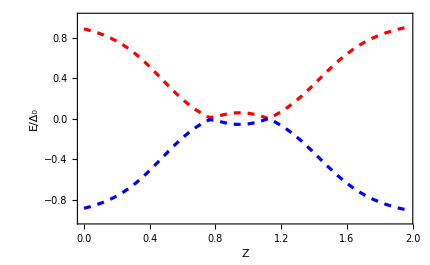

```mathematica
ListLinePlot[{listbs0[[All,{1,2}]],listbs0[[All,{1,3}]]},PlotRange->{-1,1},RotateLabel->True,FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["E/Δ_0",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
S= 1/2;
m1= -1/2;
Δ= 1.;
Ef= 50;
F= 1.;
kfa=  0.5*π;
J=1.2;
(*listbs=ParallelTable[*)
ke1=kh1=1;qp1=qm1=1;
SetSharedVariable[listbs10]
listbs10={};
ParallelDo[{

a1=1;
a2=0;
a3=0;
a4=0;
a5=-1;
a6=0;
a7=-Exp[I*kfa*ke1];
a8=0;
a9=0;
a10=0;
a11=0;
a12=0;
a13=0;
a14=0;
a15=0;
a16=0;
z1=-1;


b1=0;
b2=1;
b3=0;
b4=0;
b5=0;
b6=-1;
b7=0;
b8=-Exp[I*kfa*ke1];
b9=0;
b10=0;
b11=0;
b12=0;
b13=0;
b14=0;
b15=0;
b16=0;
z2=0;


c1=0;
c2=0;
c3=1;
c4=0;
c5=0;
c6=0;
c7=0;
c8=0;
c9=-Exp[-I*kfa*kh1];
c10=0;
c11=-1; 
c12=0; 
c13=0;
c14=0;
c15=0;
c16=0;
z3=0;


d1=0;
d2=0;
d3=0;
d4=1;
d5=0;
d6=0;
d7=0;
d8=0;
d9=0;
d10=-Exp[-I*kfa*kh1]; 
d11=0;
d12=-1;
d13=0;
d14=0;
d15=0;
d16=0;
z4=0;


e1=ke1-I*J*m1;
e2=-I*J*F;
e3=0;
e4=0;
e5=ke1;
e6=0;
e7=-ke1*Exp[I*kfa*ke1];
e8=0;
e9=0;
e10=0;
e11=0;
e12=0;
e13=0;
e14=0;
e15=0;
e16=0;
z5=ke1+I*J*m1;


f1=-I*J*F;
f2=ke1+I*J*(m1+1);
f3=0;
f4=0;
f5=0;
f6=ke1;
f7=0;
f8=-ke1*Exp[I*kfa*ke1];
f9=0;
f10=0;
f11=0;
f12=0;
f13=0;
f14=0;
f15=0;
f16=0;
z6=I*J*F;


g1=0;
g2=0;
g3=-kh1+I*J*(m1+1); (* - I*)
g4=-I*J*F;
g5=0;
g6=0;
g7=0;
g8=0;
g9=kh1*Exp[-I*kfa*kh1];
g10=0;
g11=-kh1;
g12=0;
g13=0;
g14=0;
g15=0;
g16=0;
z7=0;


h1=0;
h2=0;
h3=-I*J*F;
h4=-kh1-I*J*(m1);
h5=0;
h6=0;
h7=0;
h8=0;
h9=0;
h10=kh1*Exp[-I*kfa*kh1];
h11=0;
h12=-kh1;
h13=0;
h14=0;
h15=0;
h16=0;
z8=0;


i1=0;
i2=0;
i3=0;
i4=0;
i5=Exp[I*kfa*ke1]; 
i6=0;  
i7=1;
i8=0;
i9=0;
i10=0;
i11=0;
i12=0;
i13=-u*Exp[I*kfa*qp1]; 
i14=0;
i15=0;
i16=-v*Exp[-I*kfa*qm1]; 
z9=0;


j1=0;
j2=0;
j3=0;
j4=0;
j5=0;
j6=Exp[I*kfa*ke1];
j7=0;
j8=1;
j9=0;      
j10=0;
j11=0;
j12=0;
j13=0;
j14=-u*Exp[I*kfa*qp1];  
j15=v*Exp[-I*kfa*qm1];    
j16=0;
z10=0;


t1=0;
t2=0;
t3=0;
t4=0;
t5=0;
t6=0;
t7=0;
t8=0;
t9=1;
t10=0;
t11=Exp[-I*kfa*kh1]; 
t12=0;
t13=0;
t14=v*Exp[I*kfa*qp1];
t15=-u*Exp[-I*kfa*qm1];  
t16=0;      
z11=0;


l1=0;
l2=0;
l3=0;
l4=0;
l5=0;
l6=0;
l7=0;  
l8=0;
l9=0;
l10=1;
l11=0;
l12=Exp[-I*kfa*kh1];
l13=-v*Exp[I*kfa*qp1];
l14=0; 
l15=0;  
l16=-u*Exp[-I*kfa*qm1];
z12=0;


p1=0;
p2=0;
p3=0;
p4=0;
p5=-(ke1-I*2*Z)*Exp[I*kfa*ke1];                
p6=0; 
p7=(ke1+I*2*Z);
p8=0;
p9=0;
p10=0;
p11=0;
p12=0;
p13=u*qp1*Exp[I*kfa*qp1]; 
p14=0;
p15=0;
p16=-v*qm1*Exp[-I*kfa*qm1];
z13=0;


q1=0;
q2=0;
q3=0;
q4=0;
q5=0;
q6=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
q7=0;
q8=(ke1+I*2*Z);   
q9=0;
q10=0;
q11=0;
q12=0;
q13=0;
q14=u*qp1*Exp[I*kfa*qp1];
q15=v*qm1*Exp[-I*kfa*qm1];
q16=0;
z14=0;


r1=0;
r2=0;
r3=0;
r4=0;
r5=0;
r6=0;
r7=0;
r8=0;
r9=-(kh1-I*2*Z);
r10=0;   
r11=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
r12=0;
r13=0;
r14=-v*qp1*Exp[I*kfa*qp1];
r15=-u*qm1*Exp[-I*kfa*qm1];
r16=0; 
z15=0;


w1=0;
w2=0;
w3=0;
w4=0;
w5=0;
w6=0;
w7=0;   
w8=0;
w9=0;
w10=-(kh1-I*2*Z);
w11=0;
w12=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
w13=v*qp1*Exp[I*kfa*qp1];
w14=0;  
w15=0;  
w16=-u*qm1*Exp[-I*kfa*qm1];
z16=0;


A={{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16},{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,b16},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16},{d1,d2,d3,d4,d5,d6,d7,d8,d9,d10,d11,d12,d13,d14,d15,d16},{e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14,e15,e16},{f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16},{g1,g2,g3,g4,g5,g6,g7,g8,g9,g10,g11,g12,g13,g14,g15,g16},{h1,h2,h3,h4,h5,h6,h7,h8,h9,h10,h11,h12,h13,h14,h15,h16},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12,i13,i14,i15,i16 },{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14 ,j15 ,j16},{t1,t2,t3,t4,t5,t6,t7,t8,t9,t10,t11,t12,t13,t14 ,t15 ,t16},{l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,l11,l12,l13 ,l14,l15,l16 },{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13 ,p14,p15,p16 },{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14 ,q15 ,q16},{r1,r2,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,r13,r14 ,r15 ,r16},{w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,w11,w12,w13 ,w14,w15,w16 }}; 

B={z1,z2,z3,z4,z5,z6,z7,z8,z9,z10,z11,z12,z13,z14,z15,z16};

Sol=Refine[LinearSolve[A,B],Element[Ed,Reals]]; 

b1s=Sol[[1]]/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2) }; 
bc=Chop[b1s,10^-5];
sc0=ComplexExpand[Abs[bc]^2]/.{Arg[-1+Ed^2]-> 0,Arg[1-1/Ed^2]-> 0};
scc0=Chop[sc0,10^-5];
sct0=Together[scc0];
sd10=Denominator[sct0];
sd11=Simplify[sd10,{-1<Ed<1}];
bous0=Re[Ed]/.NSolve[sd11== 0,{Ed}][[2]];
listbs0=AppendTo[listbs10,{Z,Abs[bous0],-Abs[bous0]}]},{Z,0.001,2,0.3}];//AbsoluteTiming
listbs0=Sort[listbs10]
```

{8.59017,Null}

{{0.001,0.665948,-0.665948},{0.301,0.847321,-0.847321},{0.601,0.98727,-0.98727},{0.901,0.991899,-0.991899},{1.201,0.997455,-0.997455},{1.501,0.999038,-0.999038},{1.801,0.999615,-0.999615}}

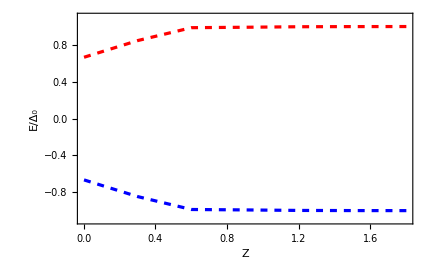

```mathematica
ListLinePlot[{listbs0[[All,{1,2}]],listbs0[[All,{1,3}]]},PlotRange->{-1.1,1.1},RotateLabel->True,FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["E/Δ_0",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

# N-sf-N-I-S (s-wave) junction

```mathematica
(*S=1/2;
Δ=1.;
Ef=50;
kfa=0.85*π;J=4.5;
m1=-1/2;
F=1;*)(*listbs=ParallelTable[*)ke1=kh1=1;qp1=qm1=1;
a1=1;
a2=0;
a3=0;
a4=0;
a5=-1;
a6=0;
a7=-Exp[I*kfa*ke1];
a8=0;
a9=0;
a10=0;
a11=0;
a12=0;
a13=0;
a14=0;
a15=0;
a16=0;
z1=-1;


b1=0;
b2=1;
b3=0;
b4=0;
b5=0;
b6=-1;
b7=0;
b8=-Exp[I*kfa*ke1];
b9=0;
b10=0;
b11=0;
b12=0;
b13=0;
b14=0;
b15=0;
b16=0;
z2=0;


c1=0;
c2=0;
c3=1;
c4=0;
c5=0;
c6=0;
c7=0;
c8=0;
c9=-Exp[-I*kfa*kh1];
c10=0;
c11=-1;
c12=0;
c13=0;
c14=0;
c15=0;
c16=0;
z3=0;


d1=0;
d2=0;
d3=0;
d4=1;
d5=0;
d6=0;
d7=0;
d8=0;
d9=0;
d10=-Exp[-I*kfa*kh1];
d11=0;
d12=-1;
d13=0;
d14=0;
d15=0;
d16=0;
z4=0;


e1=ke1-I*J*m1;
e2=-I*J*F;
e3=0;
e4=0;
e5=ke1;
e6=0;
e7=-ke1*Exp[I*kfa*ke1];
e8=0;
e9=0;
e10=0;
e11=0;
e12=0;
e13=0;
e14=0;
e15=0;
e16=0;
z5=ke1+I*J*m1;


f1=-I*J*F;
f2=ke1+I*J*(m1+1);
f3=0;
f4=0;
f5=0;
f6=ke1;
f7=0;
f8=-ke1*Exp[I*kfa*ke1];
f9=0;
f10=0;
f11=0;
f12=0;
f13=0;
f14=0;
f15=0;
f16=0;
z6=I*J*F;


g1=0;
g2=0;
g3=-kh1+I*J*(m1+1); (*-I*)
g4=-I*J*F;
g5=0;
g6=0;
g7=0;
g8=0;
g9=kh1*Exp[-I*kfa*kh1];
g10=0;
g11=-kh1;
g12=0;
g13=0;
g14=0;
g15=0;
g16=0;
z7=0;


h1=0;
h2=0;
h3=-I*J*F;
h4=-kh1-I*J*(m1);
h5=0;
h6=0;
h7=0;
h8=0;
h9=0;
h10=kh1*Exp[-I*kfa*kh1];
h11=0;
h12=-kh1;
h13=0;
h14=0;
h15=0;
h16=0;
z8=0;


i1=0;
i2=0;
i3=0;
i4=0;
i5=Exp[I*kfa*ke1];
i6=0;
i7=1;
i8=0;
i9=0;
i10=0;
i11=0;
i12=0;
i13=-u*Exp[I*kfa*qp1];
i14=0;
i15=0;
i16=-v*Exp[-I*kfa*qm1];
z9=0;


j1=0;
j2=0;
j3=0;
j4=0;
j5=0;
j6=Exp[I*kfa*ke1];
j7=0;
j8=1;
j9=0;
j10=0;
j11=0;
j12=0;
j13=0;
j14=-u*Exp[I*kfa*qp1];
j15=v*Exp[-I*kfa*qm1];
j16=0;
z10=0;


t1=0;
t2=0;
t3=0;
t4=0;
t5=0;
t6=0;
t7=0;
t8=0;
t9=1;
t10=0;
t11=Exp[-I*kfa*kh1];
t12=0;
t13=0;
t14=v*Exp[I*kfa*qp1];
t15=-u*Exp[-I*kfa*qm1];
t16=0;
z11=0;


l1=0;
l2=0;
l3=0;
l4=0;
l5=0;
l6=0;
l7=0;
l8=0;
l9=0;
l10=1;
l11=0;
l12=Exp[-I*kfa*kh1];
l13=-v*Exp[I*kfa*qp1];
l14=0;
l15=0;
l16=-u*Exp[-I*kfa*qm1];
z12=0;


p1=0;
p2=0;
p3=0;
p4=0;
p5=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
p6=0;
p7=(ke1+I*2*Z);
p8=0;
p9=0;
p10=0;
p11=0;
p12=0;
p13=u*qp1*Exp[I*kfa*qp1];
p14=0;
p15=0;
p16=-v*qm1*Exp[-I*kfa*qm1];
z13=0;


q1=0;
q2=0;
q3=0;
q4=0;
q5=0;
q6=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
q7=0;
q8=(ke1+I*2*Z);
q9=0;
q10=0;
q11=0;
q12=0;
q13=0;
q14=u*qp1*Exp[I*kfa*qp1];
q15=v*qm1*Exp[-I*kfa*qm1];
q16=0;
z14=0;


r1=0;
r2=0;
r3=0;
r4=0;
r5=0;
r6=0;
r7=0;
r8=0;
r9=-(kh1-I*2*Z);
r10=0;
r11=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
r12=0;
r13=0;
r14=-v*qp1*Exp[I*kfa*qp1];
r15=-u*qm1*Exp[-I*kfa*qm1];
r16=0;
z15=0;


w1=0;
w2=0;
w3=0;
w4=0;
w5=0;
w6=0;
w7=0;
w8=0;
w9=0;
w10=-(kh1-I*2*Z);
w11=0;
w12=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
w13=v*qp1*Exp[I*kfa*qp1];
w14=0;
w15=0;
w16=-u*qm1*Exp[-I*kfa*qm1];
z16=0;


P={{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16},{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,b16},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16},{d1,d2,d3,d4,d5,d6,d7,d8,d9,d10,d11,d12,d13,d14,d15,d16},{e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14,e15,e16},{f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16},{g1,g2,g3,g4,g5,g6,g7,g8,g9,g10,g11,g12,g13,g14,g15,g16},{h1,h2,h3,h4,h5,h6,h7,h8,h9,h10,h11,h12,h13,h14,h15,h16},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12,i13,i14,i15,i16},{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16},{t1,t2,t3,t4,t5,t6,t7,t8,t9,t10,t11,t12,t13,t14,t15,t16},{l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,l11,l12,l13,l14,l15,l16},{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13,p14,p15,p16},{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14,q15,q16},{r1,r2,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,r13,r14,r15,r16},{w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,w11,w12,w13,w14,w15,w16}};

Q={z1,z2,z3,z4,z5,z6,z7,z8,z9,z10,z11,z12,z13,z14,z15,z16};

Sol=Refine[LinearSolve[P,Q],Element[Ed,Reals]];
u=Piecewise[{{Sqrt[1/2 (1+Sqrt[(Ed^2-Δ^2)/Ed^2])],Ed^2>Δ^2},{Sqrt[1/2 (1+I Sqrt[(Δ^2-Ed^2)/Ed^2])],Ed^2<Δ^2}}];
v=Piecewise[{{Sqrt[1/2 (1-Sqrt[(Ed^2-Δ^2)/Ed^2])],Ed^2>Δ^2},{Sqrt[1/2 (1-I Sqrt[(Δ^2-Ed^2)/Ed^2])],Ed^2<Δ^2}}];
Δ=1;
B1=Abs[Sol[[1]]]^2/. {F->1,kfa->0.85 π,m1->-1/2,J->9/2};
B2=Abs[Sol[[2]]]^2/. {F->1,kfa->0.85 π,m1->-1/2,J->9/2};
A1=Abs[Sol[[3]]]^2/. {F->1,kfa->0.85 π,m1->-1/2,J->9/2};
A2=Abs[Sol[[4]]]^2/. {F->1,kfa->0.85 π,m1->-1/2,J->9/2};
A=(A1+A2);
B=(B1+B2);
```

```mathematica
S=1/2;
Δ=1.;
Ef=50;
kfa=0.85*π;J=9/2;
m11=1/2;
F1=0;
(*listbs=ParallelTable[*)
ke1=kh1=1;qp1=qm1=1;
a111=1;
a112=0;
a113=0;
a114=0;
a115=-1;
a116=0;
a117=-Exp[I*kfa*ke1];
a118=0;
a119=0;
a120=0;
a121=0;
a122=0;
a123=0;
a124=0;
a125=0;
a126=0;
z111=-1;


b111=0;
b112=1;
b113=0;
b114=0;
b115=0;
b116=-1;
b117=0;
b118=-Exp[I*kfa*ke1];
b119=0;
b120=0;
b121=0;
b122=0;
b123=0;
b124=0;
b125=0;
b126=0;
z112=0;


c111=0;
c112=0;
c113=1;
c114=0;
c115=0;
c116=0;
c117=0;
c118=0;
c119=-Exp[-I*kfa*kh1];
c120=0;
c121=-1;
c122=0;
c123=0;
c124=0;
c125=0;
c126=0;
z113=0;


d111=0;
d112=0;
d113=0;
d114=1;
d115=0;
d116=0;
d117=0;
d118=0;
d119=0;
d120=-Exp[-I*kfa*kh1];
d121=0;
d122=-1;
d123=0;
d124=0;
d125=0;
d126=0;
z114=0;


e111=ke1-I*J*m11;
e112=-I*J*F1;
e113=0;
e114=0;
e115=ke1;
e116=0;
e117=-ke1*Exp[I*kfa*ke1];
e118=0;
e119=0;
e120=0;
e121=0;
e122=0;
e123=0;
e124=0;
e125=0;
e126=0;
z115=ke1+I*J*m11;


f111=-I*J*F1;
f112=ke1+I*J*(m11+1);
f113=0;
f114=0;
f115=0;
f116=ke1;
f117=0;
f118=-ke1*Exp[I*kfa*ke1];
f119=0;
f120=0;
f121=0;
f122=0;
f123=0;
f124=0;
f125=0;
f126=0;
z116=I*J*F1;


g111=0;
g112=0;
g113=-kh1+I*J*(m11+1); (*-I*)
g114=-I*J*F1;
g115=0;
g116=0;
g117=0;
g118=0;
g119=kh1*Exp[-I*kfa*kh1];
g120=0;
g121=-kh1;
g122=0;
g123=0;
g124=0;
g125=0;
g126=0;
z117=0;


h111=0;
h112=0;
h113=-I*J*F1;
h114=-kh1-I*J*(m11);
h115=0;
h116=0;
h117=0;
h118=0;
h119=0;
h120=kh1*Exp[-I*kfa*kh1];
h121=0;
h122=-kh1;
h123=0;
h124=0;
h125=0;
h126=0;
z118=0;


i111=0;
i112=0;
i113=0;
i114=0;
i115=Exp[I*kfa*ke1];
i116=0;
i117=1;
i118=0;
i119=0;
i120=0;
i121=0;
i122=0;
i123=-u*Exp[I*kfa*qp1];
i124=0;
i125=0;
i126=-v*Exp[-I*kfa*qm1];
z119=0;


j111=0;
j112=0;
j113=0;
j114=0;
j115=0;
j116=Exp[I*kfa*ke1];
j117=0;
j118=1;
j119=0;
j120=0;
j121=0;
j122=0;
j123=0;
j124=-u*Exp[I*kfa*qp1];
j125=v*Exp[-I*kfa*qm1];
j126=0;
z120=0;


t111=0;
t112=0;
t113=0;
t114=0;
t115=0;
t116=0;
t117=0;
t118=0;
t119=1;
t120=0;
t121=Exp[-I*kfa*kh1];
t122=0;
t123=0;
t124=v*Exp[I*kfa*qp1];
t125=-u*Exp[-I*kfa*qm1];
t126=0;
z121=0;


l111=0;
l112=0;
l113=0;
l114=0;
l115=0;
l116=0;
l117=0;
l118=0;
l119=0;
l120=1;
l121=0;
l122=Exp[-I*kfa*kh1];
l123=-v*Exp[I*kfa*qp1];
l124=0;
l125=0;
l126=-u*Exp[-I*kfa*qm1];
z122=0;


p111=0;
p112=0;
p113=0;
p114=0;
p115=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
p116=0;
p117=(ke1+I*2*Z);
p118=0;
p119=0;
p120=0;
p121=0;
p122=0;
p123=u*qp1*Exp[I*kfa*qp1];
p124=0;
p125=0;
p126=-v*qm1*Exp[-I*kfa*qm1];
z123=0;


q111=0;
q112=0;
q113=0;
q114=0;
q115=0;
q116=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
q117=0;
q118=(ke1+I*2*Z);
q119=0;
q120=0;
q121=0;
q122=0;
q123=0;
q124=u*qp1*Exp[I*kfa*qp1];
q125=v*qm1*Exp[-I*kfa*qm1];
q126=0;
z124=0;


r111=0;
r112=0;
r113=0;
r114=0;
r115=0;
r116=0;
r117=0;
r118=0;
r119=-(kh1-I*2*Z);
r120=0;
r121=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
r122=0;
r123=0;
r124=-v*qp1*Exp[I*kfa*qp1];
r125=-u*qm1*Exp[-I*kfa*qm1];
r126=0;
z125=0;


w111=0;
w112=0;
w113=0;
w114=0;
w115=0;
w116=0;
w117=0;
w118=0;
w119=0;
w120=-(kh1-I*2*Z);
w121=0;
w122=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
w123=v*qp1*Exp[I*kfa*qp1];
w124=0;
w125=0;
w126=-u*qm1*Exp[-I*kfa*qm1];
z126=0;


Pu={{a111,a112,a113,a114,a115,a116,a117,a118,a119,a120,a121,a122,a123,a124,a125,a126},{b111,b112,b113,b114,b115,b116,b117,b118,b119,b120,b121,b122,b123,b124,b125,b126},{c111,c112,c113,c114,c115,c116,c117,c118,c119,c120,c121,c122,c123,c124,c125,c126},{d111,d112,d113,d114,d115,d116,d117,d118,d119,d120,d121,d122,d123,d124,d125,d126},{e111,e112,e113,e114,e115,e116,e117,e118,e119,e120,e121,e122,e123,e124,e125,e126},{f111,f112,f113,f114,f115,f116,f117,f118,f119,f120,f121,f122,f123,f124,f125,f126},{g111,g112,g113,g114,g115,g116,g117,g118,g119,g120,g121,g122,g123,g124,g125,g126},{h111,h112,h113,h114,h115,h116,h117,h118,h119,h120,h121,h122,h123,h124,h125,h126},{i111,i112,i113,i114,i115,i116,i117,i118,i119,i120,i121,i122,i123,i124,i125,i126},{j111,j112,j113,j114,j115,j116,j117,j118,j119,j120,j121,j122,j123,j124,j125,j126},{t111,t112,t113,t114,t115,t116,t117,t118,t119,t120,t121,t122,t123,t124,t125,t126},{l111,l112,l113,l114,l115,l116,l117,l118,l119,l120,l121,l122,l123,l124,l125,l126},{p111,p112,p113,p114,p115,p116,p117,p118,p119,p120,p121,p122,p123,p124,p125,p126},{q111,q112,q113,q114,q115,q116,q117,q118,q119,q120,q121,q122,q123,q124,q125,q126},{r111,r112,r113,r114,r115,r116,r117,r118,r119,r120,r121,r122,r123,r124,r125,r126},{w111,w112,w113,w114,w115,w116,w117,w118,w119,w120,w121,w122,w123,w124,w125,w126}};

Qu={z111,z112,z113,z114,z115,z116,z117,z118,z119,z120,z121,z122,z123,z124,z125,z126};

Sol1=Refine[LinearSolve[Pu,Qu],Element[Ed,Reals]];

B1u=Abs[Sol1[[1]]]^2;
B2u=Abs[Sol1[[2]]]^2;
A1u=Abs[Sol1[[3]]]^2;
A2u=Abs[Sol1[[4]]]^2;
Au=(A1u+A2u)//Simplify;
Bu=(B1u+B2u)//Simplify;
```

# Charge Conductance for Z = 0.50, 0.781 and 1.121 with respect to E/Δ_0

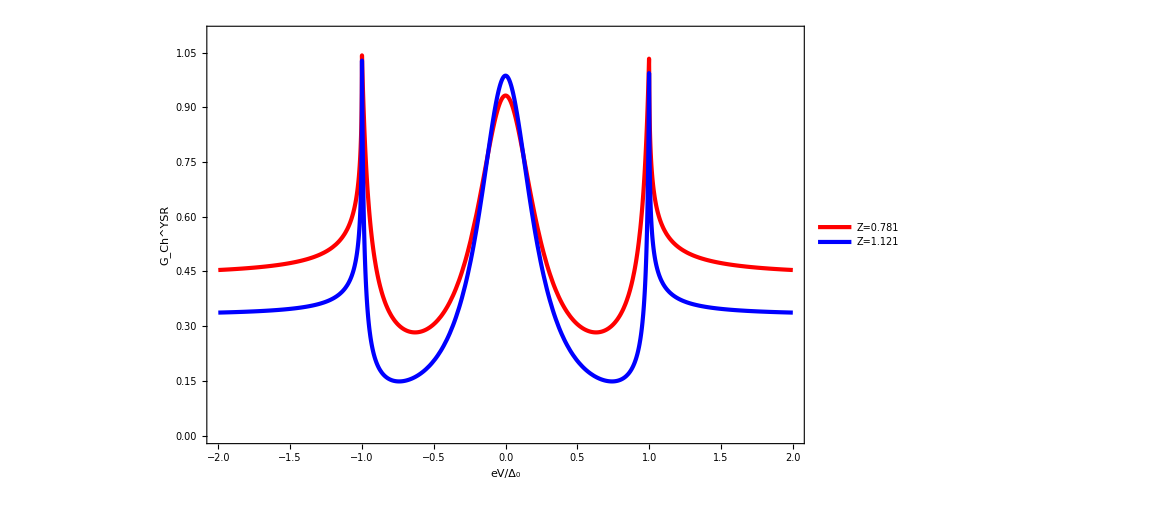

```mathematica
Plot[{(1+A-B+1+Au-Bu)/2/.{Z->0.781},(1+A-B+1+Au-Bu)/2/.{Z->1.121}},{Ed,-2,2},RotateLabel->True,PlotRange->{0,1.1},FrameLabel->{Style["eV/Δ_0",45,Bold,Black],Style[Rotate["G_Ch^YSR",270 Degree],45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,35],Frame->True,PlotLegends->Placed[{Style["Z=0.781",35,Black,Bold],Style["Z=1.121",35,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->850,LabelStyle->Directive[Bold,Black,45]]
```

# Charge Conductance for E = 0 for E/Δ_0=0.00, 0.75, 1.50 with respect to Z

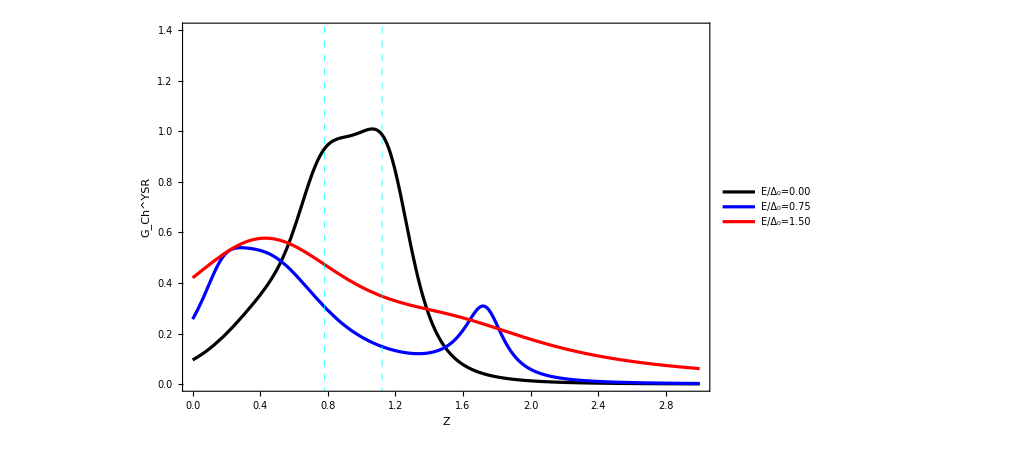

```mathematica
Plot[{(1+A-B+1+Au-Bu)/2/. {Ed->0.00001},(1+A-B+1+Au-Bu)/2/. {Ed->0.75},(1+A-B+1+Au-Bu)/2/. {Ed->1.5}},{Z,0,3},RotateLabel->True,PlotRange->{0,1.4},FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["G_Ch^YSR",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.75",16,Black,Bold],Style["E/Δ_0=1.50",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```

# Differential quantum noise at zero kelvin for Z = 0.50, 0.781, 1.121 with respect to E/Δ_0

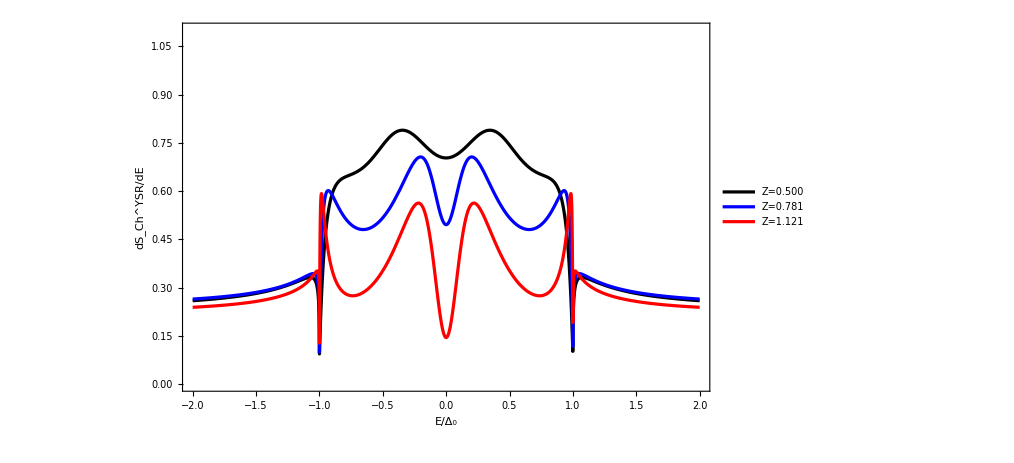

```mathematica
Plot[{(A(1-A)+B(1-B)+2A*B+Au(1-Au)+Bu(1-Bu)+2Au*Bu)/2/.{Z->0.50},(A(1-A)+B(1-B)+2A*B+Au(1-Au)+Bu(1-Bu)+2Au*Bu)/2/.{Z->0.781},(A(1-A)+B(1-B)+2A*B+Au(1-Au)+Bu(1-Bu)+2Au*Bu)/2/.{Z->1.121}},{Ed,-2,2},PlotRange->{0,1.1},RotateLabel->True,FrameLabel->{Style["E/Δ_0",25,Bold,Black],Style[Rotate["dS_Ch^YSR/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["Z=0.500",16,Black,Bold],Style["Z=0.781",16,Black,Bold],Style["Z=1.121",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15]]
```

# Differential quantum noise at zero kelvin for E/Δ_0 = 0.00, 0.75, 1.50 with respect to Z

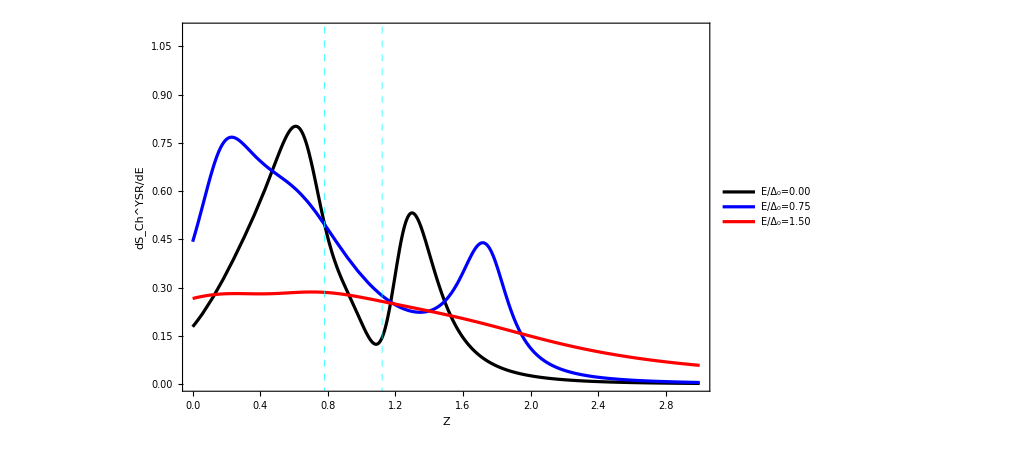

```mathematica
Plot[{(A(1-A)+B(1-B)+2A*B+Au(1-Au)+Bu(1-Bu)+2Au*Bu)/2/.{Ed->0.00001},(A(1-A)+B(1-B)+2A*B+Au(1-Au)+Bu(1-Bu)+2Au*Bu)/2/.{Ed->0.75},(A(1-A)+B(1-B)+2A*B+Au(1-Au)+Bu(1-Bu)+2Au*Bu)/2/.{Ed->1.50}},{Z,0,3},PlotRange->{0,1.1},RotateLabel->True,FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["dS_Ch^YSR/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.75",16,Black,Bold],Style["E/Δ_0=1.50",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```

# Spin conductance at zero kelvin for Z = 0.50, 0.781, 1.121 with respect to E/Δ_0

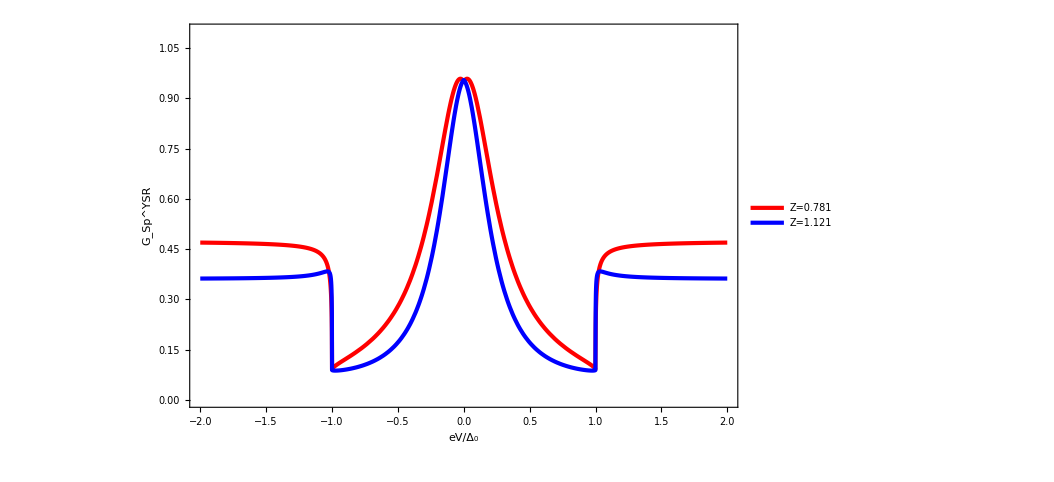

```mathematica
Plot[{(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/.{Z->0.781},(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/.{Z->1.121}},{Ed,-2,2},RotateLabel->True,PlotRange->{0,1.1},FrameLabel->{Style["eV/Δ_0",35,Bold,Black],Style[Rotate["G_Sp^YSR",270 Degree],35,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,25],Frame->True,PlotLegends->Placed[{Style["Z=0.781",30,Black,Bold],Style["Z=1.121",30,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->780,LabelStyle->Directive[Bold,Black,35]]
```

# Spin conductance at zero kelvin for E/Δ_0=0.00, 0.75, 1.50 with respect to Z

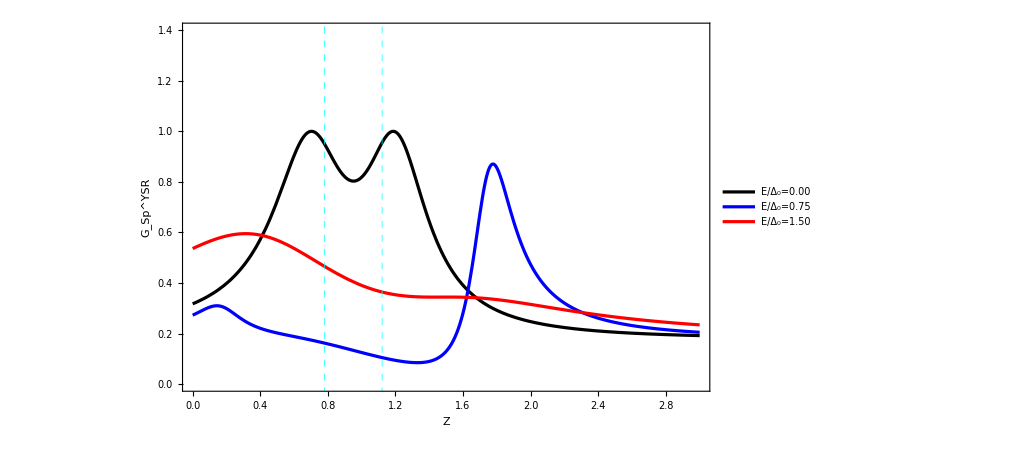

```mathematica
Plot[{(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/.{Ed->0.00001},(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/.{Ed->0.75},(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/.{Ed->1.50}},{Z,0,3},RotateLabel->True,PlotRange->{0,1.4},FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["G_Sp^YSR",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.75",16,Black,Bold],Style["E/Δ_0=1.50",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```

# Differential spin quantum noise at zero kelvin for Z=0.500,0.781 and 1.121 with respect to E/Δ_0

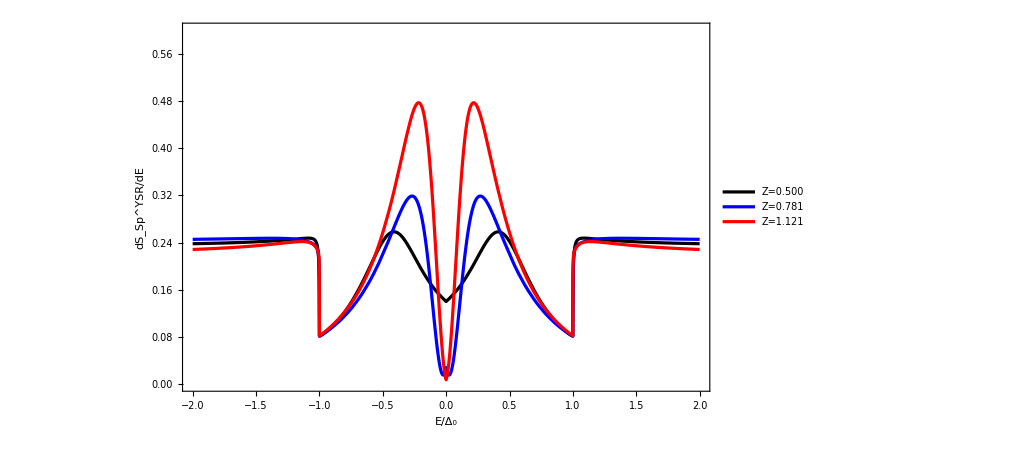

```mathematica
Plot[{(A(1-A)+B(1-B)+2A*B-4B1*A2-4B2*A1+Au(1-Au)+Bu(1-Bu)+2Au*Bu-4B1u*A2u-4B2u*A1u)/2/.{Z->0.50},(A(1-A)+B(1-B)+2A*B-4B1*A2-4B2*A1+Au(1-Au)+Bu(1-Bu)+2Au*Bu-4B1u*A2u-4B2u*A1u)/2/.{Z->0.781},(A(1-A)+B(1-B)+2A*B-4B1*A2-4B2*A1+Au(1-Au)+Bu(1-Bu)+2Au*Bu-4B1u*A2u-4B2u*A1u)/2/.{Z->1.121}},{Ed,-2,2},PlotRange->{0,0.6},RotateLabel->True,FrameLabel->{Style["E/Δ_0",25,Bold,Black],Style[Rotate["dS_Sp^YSR/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["Z=0.500",16,Black,Bold],Style["Z=0.781",16,Black,Bold],Style["Z=1.121",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15]]
```

# Differential spin quantum noise at zero kelvin for E/Δ_0=0.00, 0.75, 1.50 with respect to Z

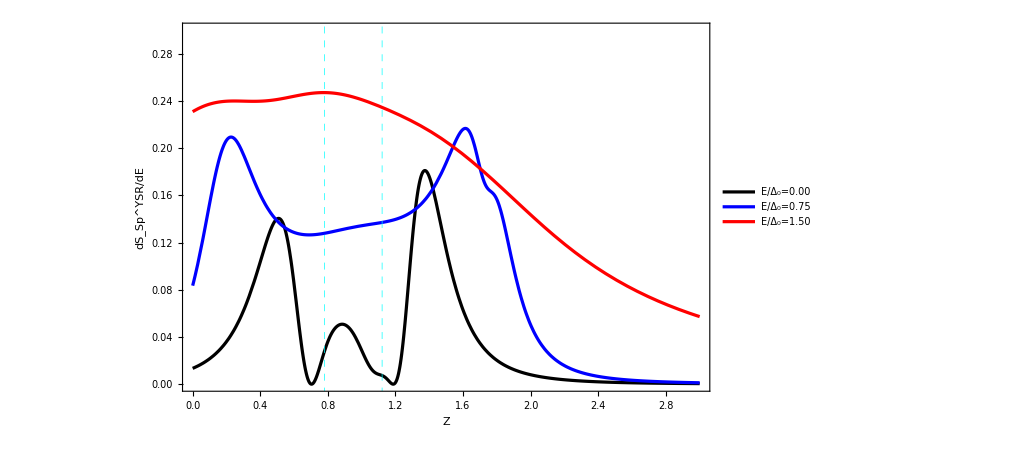

```mathematica
Plot[{(A(1-A)+B(1-B)+2A*B-4B1*A2-4B2*A1+Au(1-Au)+Bu(1-Bu)+2Au*Bu-4B1u*A2u-4B2u*A1u)/2/.{Ed->0.0001},(A(1-A)+B(1-B)+2A*B-4B1*A2-4B2*A1+Au(1-Au)+Bu(1-Bu)+2Au*Bu-4B1u*A2u-4B2u*A1u)/2/.{Ed->0.75},(A(1-A)+B(1-B)+2A*B-4B1*A2-4B2*A1+Au(1-Au)+Bu(1-Bu)+2Au*Bu-4B1u*A2u-4B2u*A1u)/2/.{Ed->1.50}},{Z,0,3},PlotRange->{0,0.3},RotateLabel->True,FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["dS_Sp^YSR/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.75",16,Black,Bold],Style["E/Δ_0=1.50",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```

# N-sf-N-I-p-wave SC (MBS bound state)

```mathematica
P=Solve[{1+ruu==tuu+fuu*Exp[I*ke*a],rud==tud+fud*Exp[I*ke*a],rauu==guu*Exp[-I*kh*a]+huu,raud==gud*Exp[-I*kh*a]+hud,I*ke(-1+ruu)-I*ke(Exp[I*ke*a]fuu-tuu)==-2*J(((1+ruu)m)/2+(rud*f)/2),I*ke*rud-I*ke(Exp[I*ke*a]fud-tud)==-2*J(((1+ruu)f)/2-rud*(m+1)/2),-I*kh*rauu+I*kh(Exp[-I*kh*a]guu-huu)==-2*J((-rauu(m+1))/2+(raud*f)/2),-I*kh(raud)+I*kh*(Exp[-I*kh*a]gud-hud)==-2J(rauu*f/2+raud*m/2),fuu+Exp[I*ke*a]tuu==cuu*Exp[I*qe*a]*u-dud*Exp[-I*qh*a]v,fud+Exp[I*ke*a]tud==cud*Exp[I*qe*a]u-duu*Exp[-I*qh*a]v,guu+Exp[-I*kh*a]huu==duu*Exp[-I*qh*a]u+cud*Exp[I*qe*a]v,gud+Exp[-I*kh*a]hud==dud*Exp[-I*qh*a]u+cuu*Exp[I*qe*a]v,I*ke(fuu-Exp[I*ke*a]tuu)+I(cuu*Exp[I*qe*a]qe*u+dud*Exp[-I*qh*a]qh*v)==2*Z*(fuu+Exp[I*ke*a]tuu),I*ke(fud-Exp[I*ke*a]tud)+I(cud*Exp[I*qe*a]qe*u+duu*Exp[-I*qh*a]qh*v)==2Z(fud+Exp[I*ke*a]tud),-I*kh(guu-Exp[-I*a*kh]huu)-I(duu*Exp[-I*qh*a]qh*u-cud*Exp[I*qe*a]qe*v)==2Z(guu+Exp[-I*kh*a]huu),-I*kh(gud-Exp[-I*a*kh]hud)-I(dud*Exp[-I*qh*a]qh*u-cuu*Exp[I*qe*a]qe*v)==2Z(gud+Exp[-I*kh*a]hud)},{ruu,tuu,fuu,rud,tud,fud,rauu,guu,huu,raud,gud,hud,cuu,dud,cud,duu}];
z1=ruu/.P[[1]];
z2=tuu/.P[[1]];
z3=fuu/.P[[1]];
z4=rud/.P[[1]];
z5=tud/.P[[1]];
z6=fud/.P[[1]];
z7=rauu/.P[[1]];
z8=guu/.P[[1]];
z9=huu/.P[[1]];
z10=raud/.P[[1]];
z11=gud/.P[[1]];
z12=hud/.P[[1]];
z13=cuu/.P[[1]];
z14=dud/.P[[1]];
z15=cud/.P[[1]];
z16=duu/.P[[1]];
Rehuu=Abs[z7]^2;
Rehud=Abs[z10]^2;
Reeuu=Abs[z1]^2;
Reeud=Abs[z4]^2;
kf=1;
a=0.85*π;
ds=1;
J=9/2;
f=Sqrt[(s-m)(s+m+1)];
Ef=30;
s=1/2;
m=-1/2;
qe=kf;
qh=kf;
ke=kf;
kh=kf;
u=Piecewise[{{Sqrt[1/2 (1+Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2 (1+I Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
v=Piecewise[{{Sqrt[1/2 (1-Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2 (1-I Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
A=Rehuu+Rehud;
B=Reeuu+Reeud;
B1=Reeuu;
B2=Reeud;
A1=Rehuu;
A2=Rehud;
A=(A1+A2);
B=(B1+B2);
```

```mathematica
P1=Solve[{1+ruu1==tuu1+fuu1*Exp[I*ke*a],rud1==tud1+fud1*Exp[I*ke*a],rauu1==guu1*Exp[-I*kh*a]+huu1,raud1==gud1*Exp[-I*kh*a]+hud1,I*ke(-1+ruu1)-I*ke(Exp[I*ke*a]fuu1-tuu1)==-2*J(((1+ruu1)1)/(2*2)+(rud1*0)/2),I*ke*rud1-I*ke(Exp[I*ke*a]fud1-tud1)==-2*J(((1+ruu1)0)/2-rud1*(1/2+1)/2),-I*kh*rauu1+I*kh(Exp[-I*kh*a]guu1-huu1)==-2*J((-rauu1(1/2+1))/2+(raud1*0)/2),-I*kh(raud1)+I*kh*(Exp[-I*kh*a]gud1-hud1)==-2J(rauu1*0/2+raud1*1/4),fuu1+Exp[I*ke*a]tuu1==cuu1*Exp[I*qe*a]*u-dud1*Exp[-I*qh*a]v,fud1+Exp[I*ke*a]tud1==cud1*Exp[I*qe*a]u-duu1*Exp[-I*qh*a]v,guu1+Exp[-I*kh*a]huu1==duu1*Exp[-I*qh*a]u+cud1*Exp[I*qe*a]v,gud1+Exp[-I*kh*a]hud1==dud1*Exp[-I*qh*a]u+cuu1*Exp[I*qe*a]v,I*ke(fuu1-Exp[I*ke*a]tuu1)+I(cuu1*Exp[I*qe*a]qe*u+dud1*Exp[-I*qh*a]qh*v)==2*Z*(fuu1+Exp[I*ke*a]tuu1),I*ke(fud1-Exp[I*ke*a]tud1)+I(cud1*Exp[I*qe*a]qe*u+duu1*Exp[-I*qh*a]qh*v)==2Z(fud1+Exp[I*ke*a]tud1),-I*kh(guu1-Exp[-I*a*kh]huu1)-I(duu1*Exp[-I*qh*a]qh*u-cud1*Exp[I*qe*a]qe*v)==2Z(guu1+Exp[-I*kh*a]huu1),-I*kh(gud1-Exp[-I*a*kh]hud1)-I(dud1*Exp[-I*qh*a]qh*u-cuu1*Exp[I*qe*a]qe*v)==2Z(gud1+Exp[-I*kh*a]hud1)},{ruu1,tuu1,fuu1,rud1,tud1,fud1,rauu1,guu1,huu1,raud1,gud1,hud1,cuu1,dud1,cud1,duu1}];
z111=ruu1/.P1[[1]];
z112=tuu1/.P1[[1]];
z113=fuu1/.P1[[1]];
z114=rud1/.P1[[1]];
z115=tud1/.P1[[1]];
z116=fud1/.P1[[1]];
z117=rauu1/.P1[[1]];
z118=guu1/.P1[[1]];
z119=huu1/.P1[[1]];
z120=raud1/.P1[[1]];
z121=gud1/.P1[[1]];
z122=hud1/.P1[[1]];
z123=cuu1/.P1[[1]];
z124=dud1/.P1[[1]];
z125=cud1/.P1[[1]];
z126=duu1/.P1[[1]];
Rehuu1=Abs[z117]^2;
Rehud1=Abs[z120]^2;
Reeuu1=Abs[z111]^2;
Reeud1=Abs[z114]^2;
kf=1;
a=0.85*π;
ds=1;
J=9/2;
f=Sqrt[(s-m)(s+m+1)];
Ef=30;
s=1/2;
m=1/2;
qe=kf;
qh=kf;
ke=kf;
kh=kf;
u=Piecewise[{{Sqrt[1/2 (1+Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2 (1+I Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
v=Piecewise[{{Sqrt[1/2 (1-Sqrt[(G^2-ds^2)/G^2])],G^2>ds^2},{Sqrt[1/2 (1-I Sqrt[(ds^2-G^2)/G^2])],G^2<ds^2}}];
A=Rehuu1+Rehud1;
B=Reeuu1+Reeud1;
B1u=Reeuu1;
B2u=Reeud1;
A1u=Rehuu1;
A2u=Rehud1;
Au=(A1u+A2u)//Simplify;
Bu=(B1u+B2u)//Simplify;
```

```mathematica
SetSharedVariable[listbs10]
listbs10={};
ParallelDo[{Q1=(1+A-B+1+Au-Bu)/2/. {G->0.00001};
Q2=(1+A-B+1+Au-Bu)/2/. {G->0.75};
Q3=(1+A-B+1+Au-Bu)/2/. {G->1.50};
Q4=(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/. {G->0.00001};
Q5=(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/. {G->0.75};
Q6=(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/. {G->1.50};
Q7=(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/. {G->0.00001};
Q8=(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/. {G->0.75};
Q9=(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/. {G->1.50};
Q10=(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/. {G->0.00001};
Q11=(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/. {G->0.75};
Q12=(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/. {G->1.50};
listbs0=AppendTo[listbs10,{Z,Q1,Q2,Q3,Q4,Q5,Q6,Q7,Q8,Q9,Q10,Q11,Q12}]},{Z,0.001,3,0.04}];//AbsoluteTiming
listbs0=Sort[listbs10];
Export["cond1.dat",listbs0]
```

{95.3236,Null}

cond1.dat

# Charge Conductance for Z = 0.50, 0.781 and 1.121 with respect to E/Δ_0 for s=1/2, m = -1/2

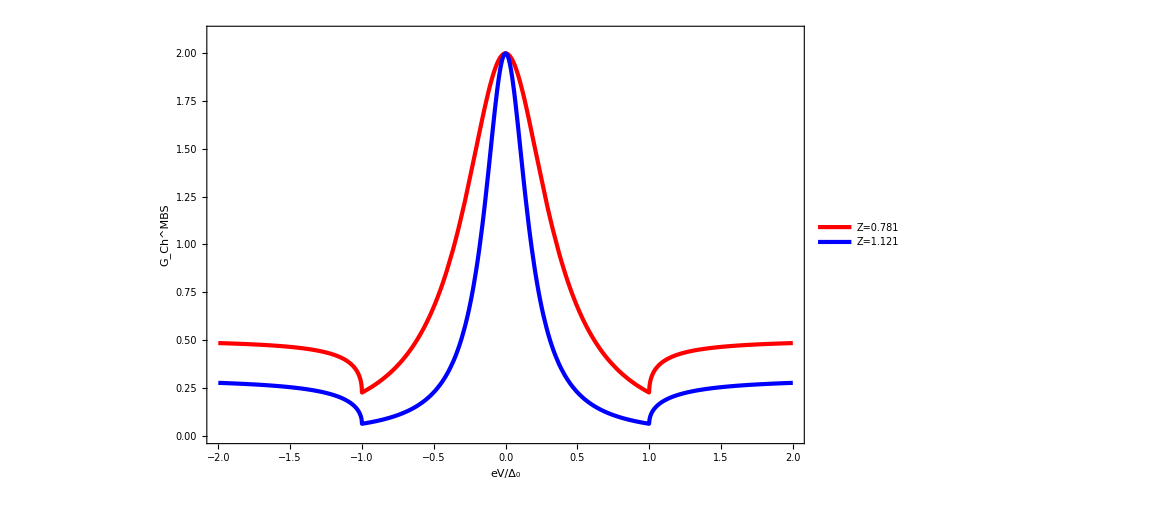

```mathematica
Plot[{(1+A-B+1+Au-Bu)/2/.{Z->0.781},(1+A-B+1+Au-Bu)/2/.{Z->1.121}},{G,-2,2},RotateLabel->True,PlotRange->{0,2.1},FrameLabel->{Style["eV/Δ_0",45,Bold,Black],Style[Rotate["G_Ch^MBS",270 Degree],45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,35],Frame->True,PlotLegends->Placed[{Style["Z=0.781",35,Black,Bold],Style["Z=1.121",35,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->850,LabelStyle->Directive[Bold,Black,45]]
```

# Charge Conductance for E = 0 for E/Δ_0=0.00, 0.75, 1.50 with respect to Z for s=1/2, m = -1/2

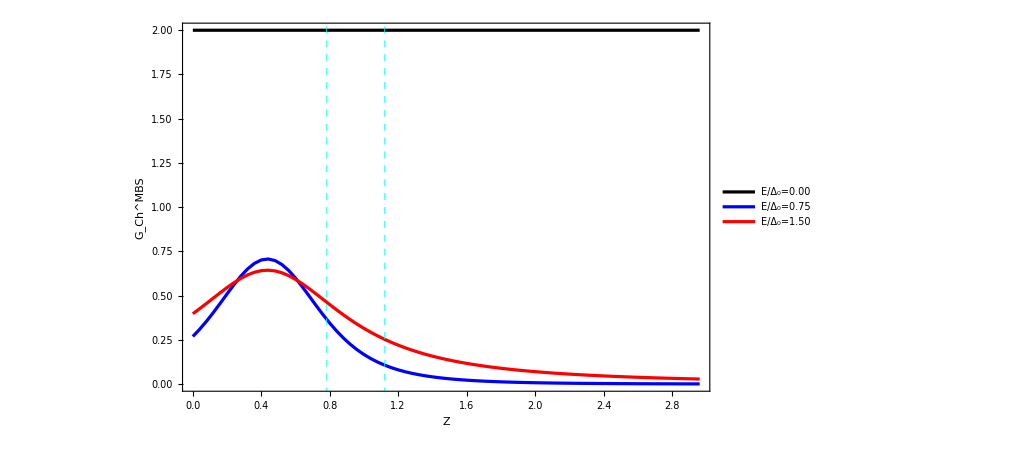

```mathematica
data1=Import["cond1.dat"][[All,{1,2}]];
data2=Import["cond1.dat"][[All,{1,3}]];
data3=Import["cond1.dat"][[All,{1,4}]];
ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,Frame->True,RotateLabel->True,FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["G_Ch^MBS",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.75",16,Black,Bold],Style["E/Δ_0=1.50",16,Black,Bold],Style["helical-p without SOC",16,Black,Bold],Style["helical-p with SOC",16,Black,Bold]},{Right,Center}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```

# Differential quantum noise at zero kelvin for Z = 0.50, 0.781, 1.121 with respect to E/Δ_0 for s=1/2, m = -1/2

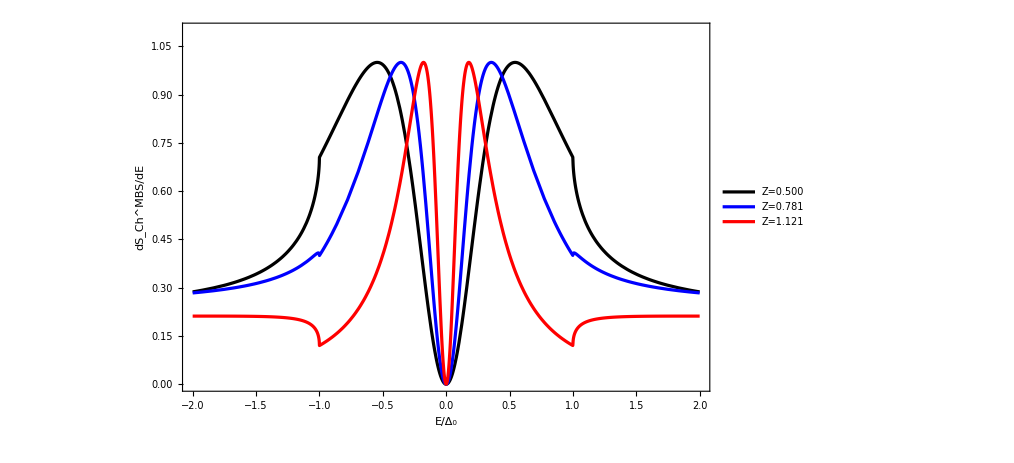

```mathematica
Plot[{(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/.{Z->0.50},(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/.{Z->0.781},(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/.{Z->1.121}},{G,-2,2},PlotRange->{0,1.1},RotateLabel->True,FrameLabel->{Style["E/Δ_0",25,Bold,Black],Style[Rotate["dS_Ch^MBS/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["Z=0.500",16,Black,Bold],Style["Z=0.781",16,Black,Bold],Style["Z=1.121",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15]]
```

# Differential quantum noise at zero kelvin for E/Δ_0 = 0.00, 0.75, 1.50 with respect to Z for s=1/2, m = -1/2

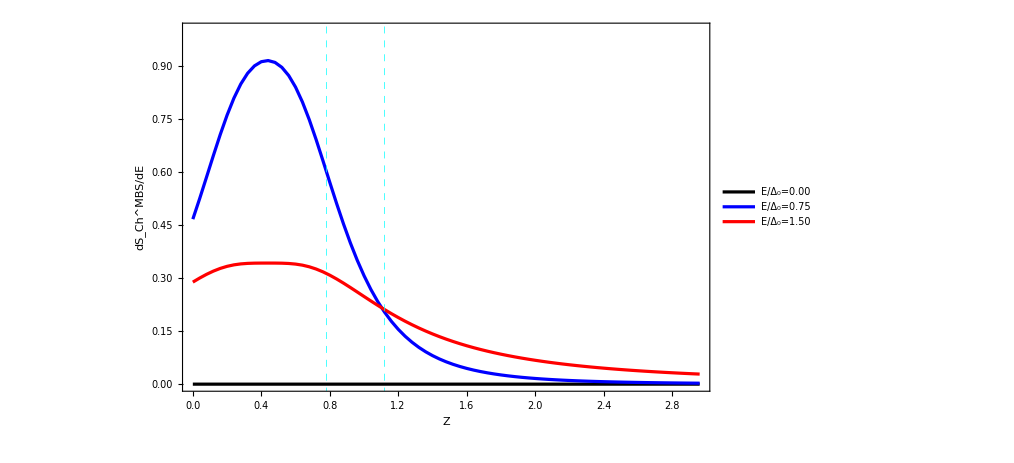

```mathematica
data1=Import["cond1.dat"][[All,{1,5}]];
data2=Import["cond1.dat"][[All,{1,6}]];
data3=Import["cond1.dat"][[All,{1,7}]];
ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{0,1.0},RotateLabel->True,FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["dS_Ch^MBS/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.75",16,Black,Bold],Style["E/Δ_0=1.50",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```

# Spin conductance at zero kelvin for Z = 0.50, 0.781, 1.121 with respect to E/Δ_0 for s=1/2, m = -1/2

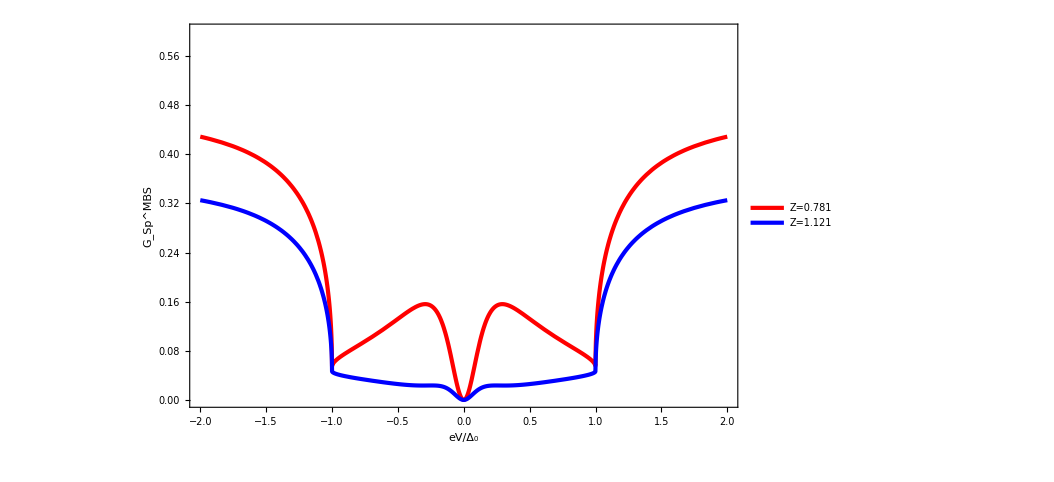

```mathematica
Plot[{(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/.{Z->0.781},(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/.{Z->1.121}},{G,-2,2},RotateLabel->True,PlotRange->{0,0.6},FrameLabel->{Style["eV/Δ_0",35,Bold,Black],Style[Rotate["G_Sp^MBS",270 Degree],35,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,25],Frame->True,PlotLegends->Placed[{Style["Z=0.781",30,Black,Bold],Style["Z=1.121",30,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->780,LabelStyle->Directive[Bold,Black,35]]
```

# Spin conductance at zero kelvin for E/Δ_0=0.00, 0.75, 1.50 with respect to Z for s=1/2, m = -1/2

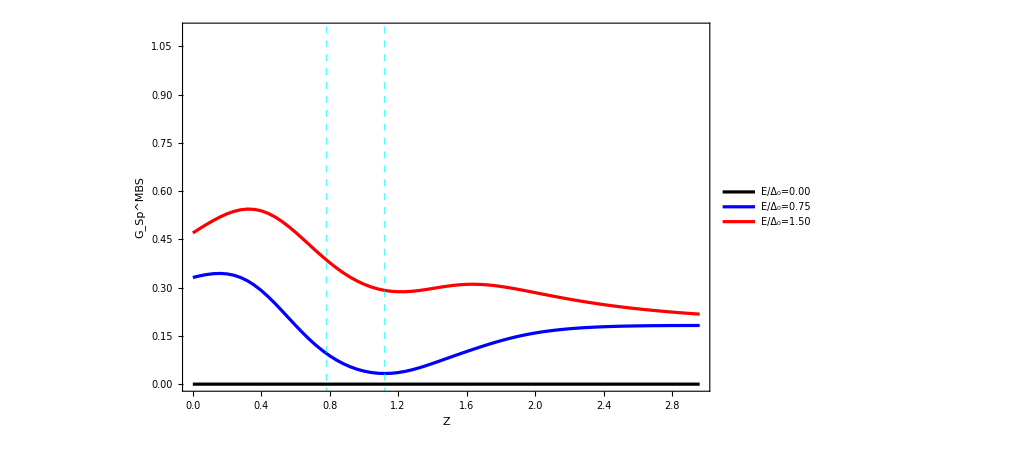

```mathematica
data1=Import["cond1.dat"][[All,{1,8}]];
data2=Import["cond1.dat"][[All,{1,9}]];
data3=Import["cond1.dat"][[All,{1,10}]];
ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{0,1.1},RotateLabel->True,PlotRange->{0,0.6},FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["G_Sp^MBS",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.75",16,Black,Bold],Style["E/Δ_0=1.50",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```

# Differential spin quantum noise at zero kelvin for Z=0.500,0.781 and 1.121 with respect to E/Δ_0 for s=1/2, m = -1/2

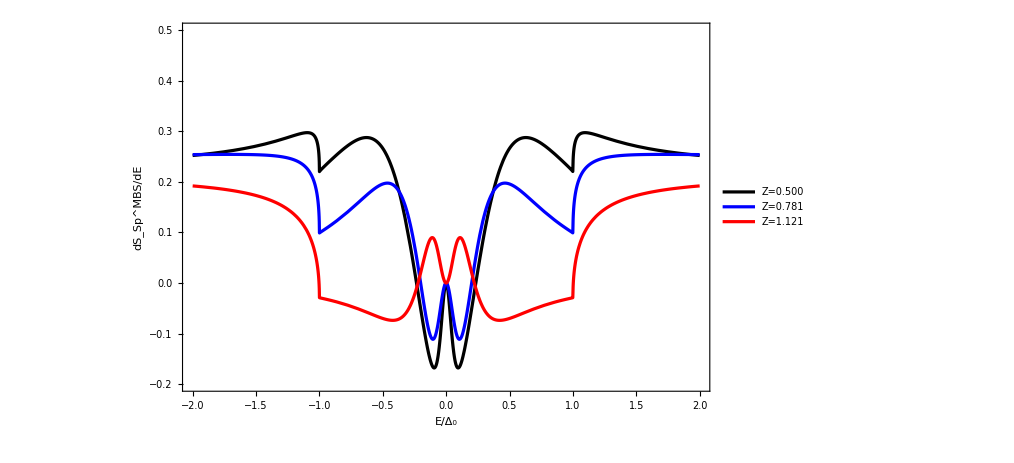

```mathematica
Plot[{(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/.{Z->0.50},(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/.{Z->0.781},(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/.{Z->1.121}},{G,-2,2},PlotRange->{-0.2,0.5},RotateLabel->True,FrameLabel->{Style["E/Δ_0",25,Bold,Black],Style[Rotate["dS_Sp^MBS/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["Z=0.500",16,Black,Bold],Style["Z=0.781",16,Black,Bold],Style["Z=1.121",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15]]
```

# Differential spin quantum noise at zero kelvin for E/Δ_0=0.00,0.75 and 1.50 with respect to Z for s=1/2, m = -1/2

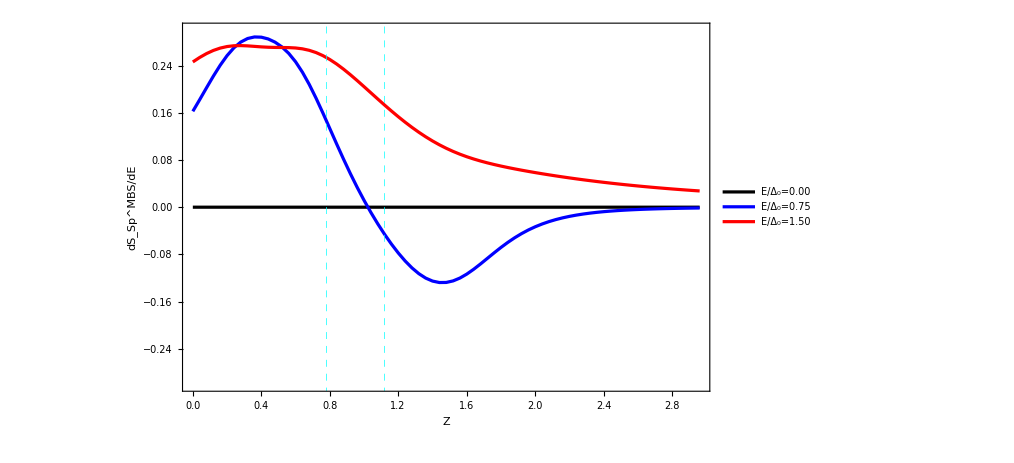

```mathematica
data1=Import["cond1.dat"][[All,{1,11}]];
data2=Import["cond1.dat"][[All,{1,12}]];
data3=Import["cond1.dat"][[All,{1,13}]];
ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{-0.3,0.3},RotateLabel->True,FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["dS_Sp^MBS/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.75",16,Black,Bold],Style["E/Δ_0=1.50",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```

# N-sf-N-I-spin-less p-wave SC (MBS bound state) with spin-flip scattering

```mathematica
P=Solve[{1+reeuu==beeuu1 ⅇ^(ⅈ a)+teeuu1,reeud==beeud1 ⅇ^(ⅈ a)+teeud1,rehud==aehud1+cehud1 ⅇ^(-ⅈ a),rehuu==aehuu1+cehuu1 ⅇ^(-ⅈ a),ⅈ J (m+f reeud+m reeuu)==2 (-1-beeuu1 ⅇ^(ⅈ a)+reeuu+teeuu1),ⅈ J (f-m reeud+f reeuu)==2 (-beeud1 ⅇ^(ⅈ a)+reeud+teeud1),ⅈ J (m rehud-f rehuu)==2 (aehud1-cehud1 ⅇ^(-ⅈ a)+rehud),-ⅈ J (f rehud+m rehuu)==2 (aehuu1-cehuu1 ⅇ^(-ⅈ a)+rehuu),beeuu1+ⅇ^(ⅈ a) teeuu1==nm teeuu+np tehuu,beeud1+ⅇ^(ⅈ a) teeud1==nm teeud+np tehud,cehud1+aehud1 ⅇ^(-ⅈ a)==teeud+tehud,cehuu1+aehuu1 ⅇ^(-ⅈ a)==teeuu+tehuu,2 beeuu1+dp teeuu+2 km nm teeuu-2 ⅇ^(ⅈ a) teeuu1+dp tehuu+2 kp np tehuu==-2 ⅈ (beeuu1+ⅇ^(ⅈ a) teeuu1) Z,2 beeud1+dp teeud+2 km nm teeud-2 ⅇ^(ⅈ a) teeud1+dp tehud+2 kp np tehud==-2 ⅈ (beeud1+ⅇ^(ⅈ a) teeud1) Z,2 cehud1-2 aehud1 ⅇ^(-ⅈ a)-2 km teeud+dp nm teeud-2 kp tehud+dp np tehud==2 ⅈ (cehud1+aehud1 ⅇ^(-ⅈ a)) Z,2 cehuu1-2 aehuu1 ⅇ^(-ⅈ a)-2 km teeuu+dp nm teeuu-2 kp tehuu+dp np tehuu==2 ⅈ (cehuu1+aehuu1 ⅇ^(-ⅈ a)) Z},{reeuu,beeuu1,teeuu1,reeud,beeud1,teeud1,rehud,aehud1,cehud1,rehuu,aehuu1,cehuu1,teeuu,tehuu,teeud,tehud}];
a=0.85*π;
z1=reeuu/.P[[1]];
z2=beeuu1/.P[[1]];
z3=teeuu1/.P[[1]];
z4=reeud/.P[[1]];
z5=beeud1/.P[[1]];
z6=teeud1/.P[[1]];
z7=rehud/.P[[1]];
z8=aehud1/.P[[1]];
z9=cehud1/.P[[1]];
z10=rehuu/.P[[1]];
z11=aehuu1/.P[[1]];
z12=cehuu1/.P[[1]];
z13=teeuu/.P[[1]];
z14=tehuu/.P[[1]];
z15=teeud/.P[[1]];
z16=tehud/.P[[1]];
Rehuu=Abs[z7]^2;
Rehud=Abs[z10]^2;
Reeuu=Abs[z1]^2;
Reeud=Abs[z4]^2;
m=-1/2;
f=1;
J=4.5;
mp=1;
dp=0.07;
kp=0.00707107  Sqrt[19951.+Sqrt[-1.9576*10^6+4.*10^8 G^2*dp^2]];
km=-0.00707107  Sqrt[19951.-1. Sqrt[-1.9576*10^6+4.*10^8 G^2*dp^2]];
np=Piecewise[{{(G*dp+kp^2-mp)/(dp*kp),G>0},{(-G*dp+kp^2-mp)/(dp*kp),G<0}}];
nm=Piecewise[{{(G*dp+km^2-mp)/(dp*km),G>0},{(-G*dp+km^2-mp)/(dp*km),G<0}}];
(*np=Piecewise[{{(G*dp+kp^2-mp)/(dp*kp),G>=0},{(-G*dp+kp^2-mp)/(dp*kp),G<0}}];
nm=Piecewise[{{(G*dp+km^2-mp)/(dp*km),G>=0},{(-G*dp+km^2-mp)/(dp*km),G<0}}];*)
(*kp=0.00707107  Sqrt[151.+Sqrt[-17199.+4.*10^8 G^2]];
km=0.007071067811865476 √(151.-1. √(-17199.+4.*^8 G^2));*)
A=Rehuu+Rehud;
B=Reeuu+Reeud;
B1=Reeuu;
B2=Reeud;
A1=Rehuu;
A2=Rehud;
A=(A1+A2);
B=(B1+B2);
```

```mathematica
P=Solve[{1+reeuu1==beeuu11 ⅇ^(ⅈ a)+teeuu11,reeud1==beeud11 ⅇ^(ⅈ a)+teeud11,rehud1==aehud11+cehud11 ⅇ^(-ⅈ a),rehuu1==aehuu11+cehuu11 ⅇ^(-ⅈ a),ⅈ J (1/2+0* reeud1+1/2* reeuu1)==2 (-1-beeuu11 ⅇ^(ⅈ a)+reeuu1+teeuu11),ⅈ J (0-1/2* reeud1+0 reeuu1)==2 (-beeud11 ⅇ^(ⅈ a)+reeud1+teeud11),ⅈ J (1/2* rehud1-0* rehuu1)==2 (aehud11-cehud11 ⅇ^(-ⅈ a)+rehud1),-ⅈ J (0* rehud1+1/2* rehuu1)==2 (aehuu11-cehuu11 ⅇ^(-ⅈ a)+rehuu1),beeuu11+ⅇ^(ⅈ a) teeuu11==nm teeuu1+np tehuu1,beeud11+ⅇ^(ⅈ a) teeud11==nm teeud1+np tehud1,cehud11+aehud11 ⅇ^(-ⅈ a)==teeud1+tehud1,cehuu11+aehuu11 ⅇ^(-ⅈ a)==teeuu1+tehuu1,2 beeuu11+dp teeuu1+2 km nm teeuu1-2 ⅇ^(ⅈ a) teeuu11+dp tehuu1+2 kp np tehuu1==-2 ⅈ (beeuu11+ⅇ^(ⅈ a) teeuu11) Z,2 beeud11+dp teeud1+2 km nm teeud1-2 ⅇ^(ⅈ a) teeud11+dp tehud1+2 kp np tehud1==-2 ⅈ (beeud11+ⅇ^(ⅈ a) teeud11) Z,2 cehud11-2 aehud11 ⅇ^(-ⅈ a)-2 km teeud1+dp nm teeud1-2 kp tehud1+dp np tehud1==2 ⅈ (cehud11+aehud11 ⅇ^(-ⅈ a)) Z,2 cehuu11-2 aehuu11 ⅇ^(-ⅈ a)-2 km teeuu1+dp nm teeuu1-2 kp tehuu1+dp np tehuu1==2 ⅈ (cehuu11+aehuu11 ⅇ^(-ⅈ a)) Z},{reeuu1,beeuu11,teeuu11,reeud1,beeud11,teeud11,rehud1,aehud11,cehud11,rehuu1,aehuu11,cehuu11,teeuu1,tehuu1,teeud1,tehud1}];
a=0.85*π;
z111=reeuu1/.P[[1]];
z112=beeuu11/.P[[1]];
z113=teeuu11/.P[[1]];
z114=reeud1/.P[[1]];
z115=beeud11/.P[[1]];
z116=teeud11/.P[[1]];
z117=rehud1/.P[[1]];
z118=aehud11/.P[[1]];
z119=cehud11/.P[[1]];
z120=rehuu1/.P[[1]];
z121=aehuu11/.P[[1]];
z122=cehuu11/.P[[1]];
z123=teeuu1/.P[[1]];
z124=tehuu1/.P[[1]];
z125=teeud1/.P[[1]];
z126=tehud1/.P[[1]];
Rehuu1=Abs[z117]^2;
Rehud1=Abs[z120]^2;
Reeuu1=Abs[z111]^2;
Reeud1=Abs[z114]^2;
J=4.5;
mp=1;
dp=0.07;
kp=0.00707107  Sqrt[19951.+Sqrt[-1.9576*10^6+4.*10^8 G^2*dp^2]];
km=-0.00707107  Sqrt[19951.-1. Sqrt[-1.9576*10^6+4.*10^8 G^2*dp^2]];
np=Piecewise[{{(G*dp+kp^2-mp)/(dp*kp),G>0},{(-G*dp+kp^2-mp)/(dp*kp),G<0}}];
nm=Piecewise[{{(G*dp+km^2-mp)/(dp*km),G>0},{(-G*dp+km^2-mp)/(dp*km),G<0}}];
B1u=Reeuu1;
B2u=Reeud1;
A1u=Rehuu1;
A2u=Rehud1;
Au=A1u+A2u;
Bu=B1u+B2u;
```

```mathematica
SetSharedVariable[listbs10]
listbs10={};
ParallelDo[{Q1=(1+A-B+1+Au-Bu)/2/. {G->0.00001};
Q2=(1+A-B+1+Au-Bu)/2/. {G->0.75};
Q3=(1+A-B+1+Au-Bu)/2/. {G->1.50};
Q4=(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/. {G->0.00001};
Q5=(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/. {G->0.75};
Q6=(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/. {G->1.50};
Q7=(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/. {G->0.00001};
Q8=(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/. {G->0.75};
Q9=(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/. {G->1.50};
Q10=(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/. {G->0.00001};
Q11=(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/. {G->0.75};
Q12=(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/. {G->1.50};
listbs0=AppendTo[listbs10,{Z,Q1,Q2,Q3,Q4,Q5,Q6,Q7,Q8,Q9,Q10,Q11,Q12}]},{Z,0.001,3,0.04}];//AbsoluteTiming
listbs0=Sort[listbs10];
Export["cond3.dat",listbs0]
```

{40.16,Null}

cond3.dat

# Charge Conductance for Z = 0.50, 0.781 and 1.121 with respect to E/Δ_0 for s=1/2, m = -1/2

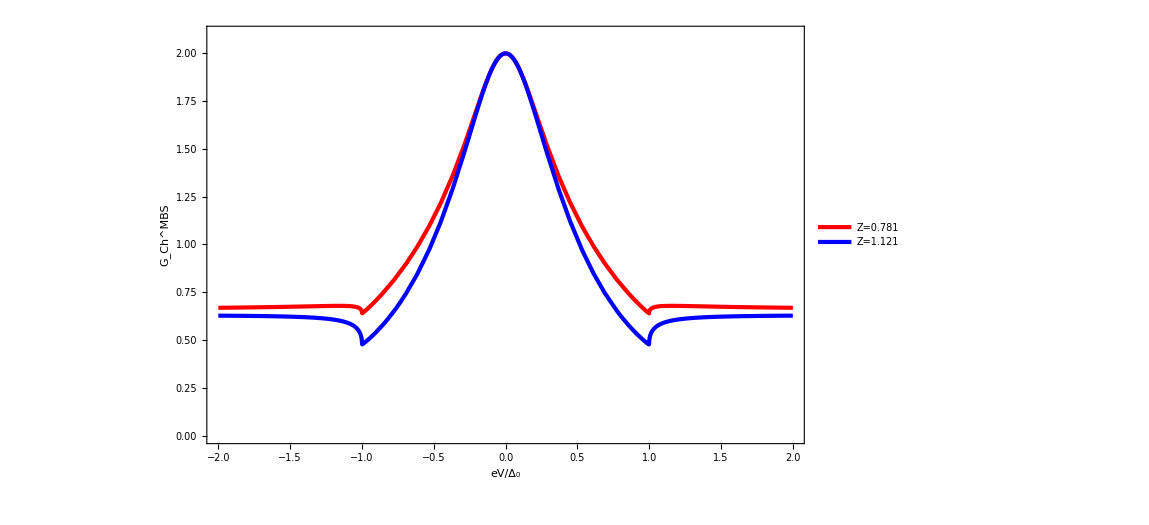

```mathematica
Plot[{(1+A-B+1+Au-Bu)/2/.{Z->0.781},(1+A-B+1+Au-Bu)/2/.{Z->1.121}},{G,-2,2},RotateLabel->True,PlotRange->{0,2.1},FrameLabel->{Style["eV/Δ_0",45,Bold,Black],Style[Rotate["G_Ch^MBS",270 Degree],45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,35],Frame->True,PlotLegends->Placed[{Style["Z=0.781",35,Black,Bold],Style["Z=1.121",35,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->850,LabelStyle->Directive[Bold,Black,45]]
```

# Charge Conductance for E/Δ_0=0.00, 0.75, 1.50 with respect to Z for s=1/2, m = -1/2

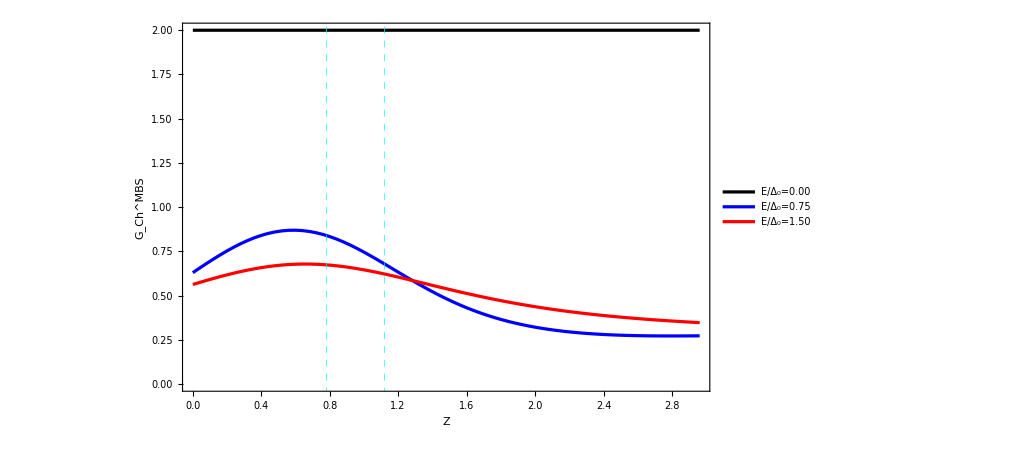

```mathematica
data1=Import["cond3.dat"][[All,{1,2}]];
data2=Import["cond3.dat"][[All,{1,3}]];
data3=Import["cond3.dat"][[All,{1,4}]];
ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,Frame->True,RotateLabel->True,FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["G_Ch^MBS",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.75",16,Black,Bold],Style["E/Δ_0=1.50",16,Black,Bold],Style["helical-p without SOC",16,Black,Bold],Style["helical-p with SOC",16,Black,Bold]},{Right,Center}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```

# Differential quantum noise at zero kelvin for Z = 0.50, 0.781, 1.121 with respect to E/Δ_0 for s=1/2, m = -1/2

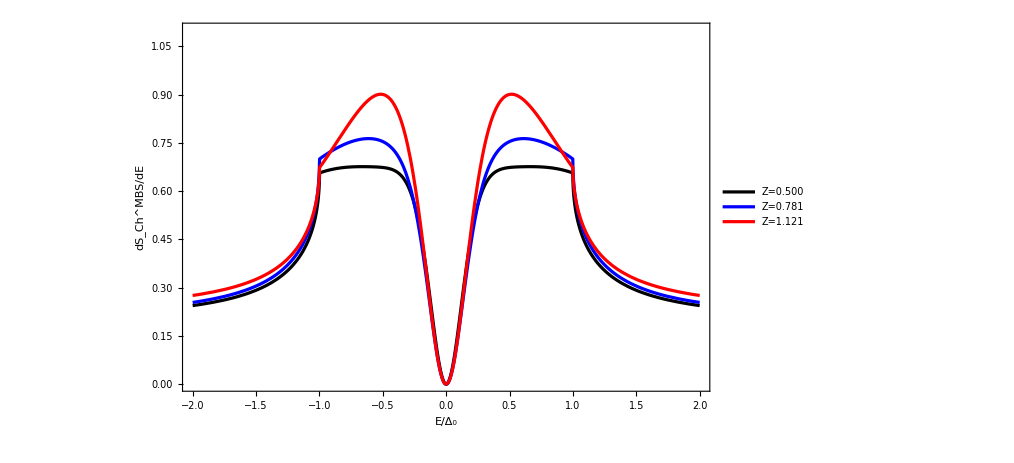

```mathematica
Plot[{(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/.{Z->0.50},(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/.{Z->0.781},(A (1-A)+B (1-B)+2 A*B+Au (1-Au)+Bu (1-Bu)+2 Au*Bu)/2/.{Z->1.121}},{G,-2,2},PlotRange->{0,1.1},RotateLabel->True,FrameLabel->{Style["E/Δ_0",25,Bold,Black],Style[Rotate["dS_Ch^MBS/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["Z=0.500",16,Black,Bold],Style["Z=0.781",16,Black,Bold],Style["Z=1.121",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15]]
```

# Differential quantum noise at zero kelvin for E/Δ_0 = 0.00, 0.75, 1.50 with respect to Z for s=1/2, m = -1/2

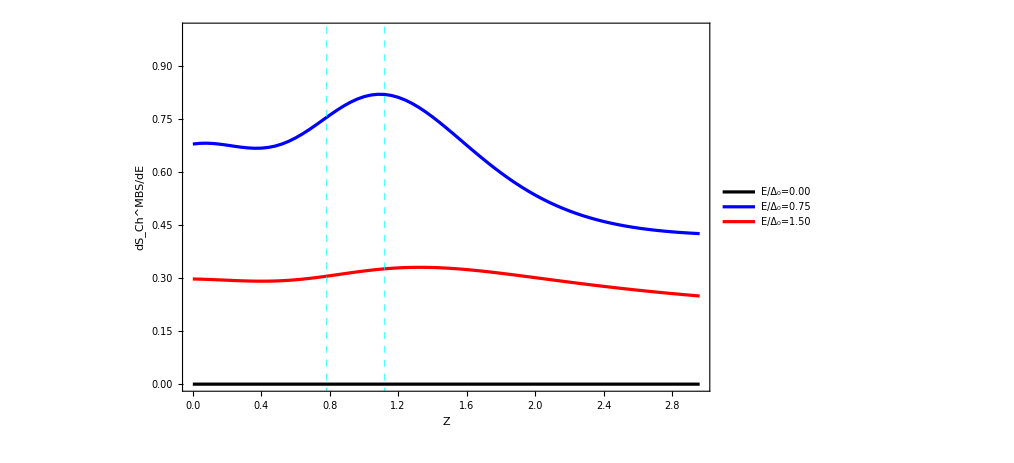

```mathematica
data1=Import["cond3.dat"][[All,{1,5}]];
data2=Import["cond3.dat"][[All,{1,6}]];
data3=Import["cond3.dat"][[All,{1,7}]];
ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{0,1},RotateLabel->True,FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["dS_Ch^MBS/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.75",16,Black,Bold],Style["E/Δ_0=1.50",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```

# Spin conductance at zero kelvin for Z = 0.50, 0.781, 1.121 with respect to E/Δ_0 for s=1/2, m = -1/2

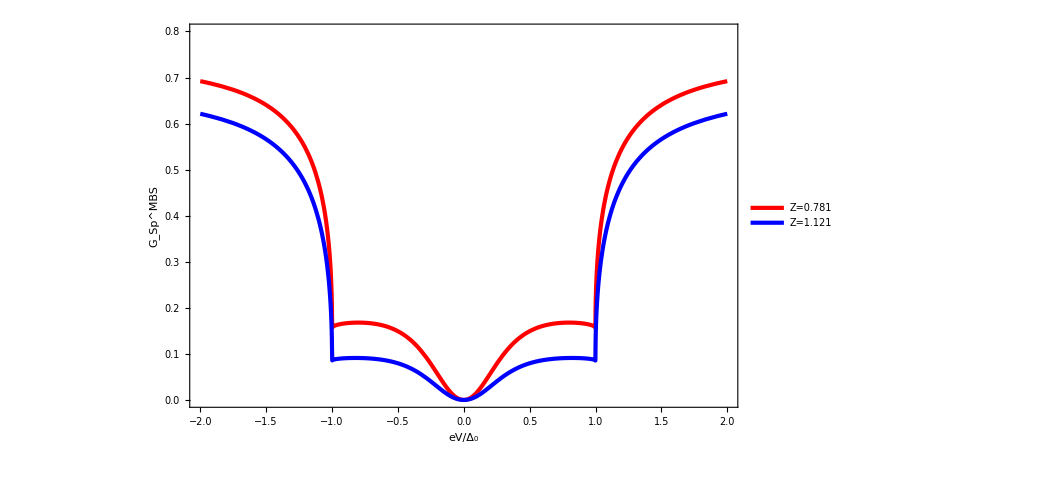

```mathematica
Plot[{(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/.{Z->0.781},(1-A2+A1-B1+B2+1-A2u+A1u-B1u+B2u)/2/.{Z->1.121}},{G,-2,2},RotateLabel->True,PlotRange->{0,0.8},FrameLabel->{Style["eV/Δ_0",35,Bold,Black],Style[Rotate["G_Sp^MBS",270 Degree],35,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,25],Frame->True,PlotLegends->Placed[{Style["Z=0.781",30,Black,Bold],Style["Z=1.121",30,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->780,LabelStyle->Directive[Bold,Black,35]]
```

# Spin conductance at zero kelvin for E/Δ_0=0.00, 0.75, 1.50 with respect to Z for s=1/2, m = -1/2

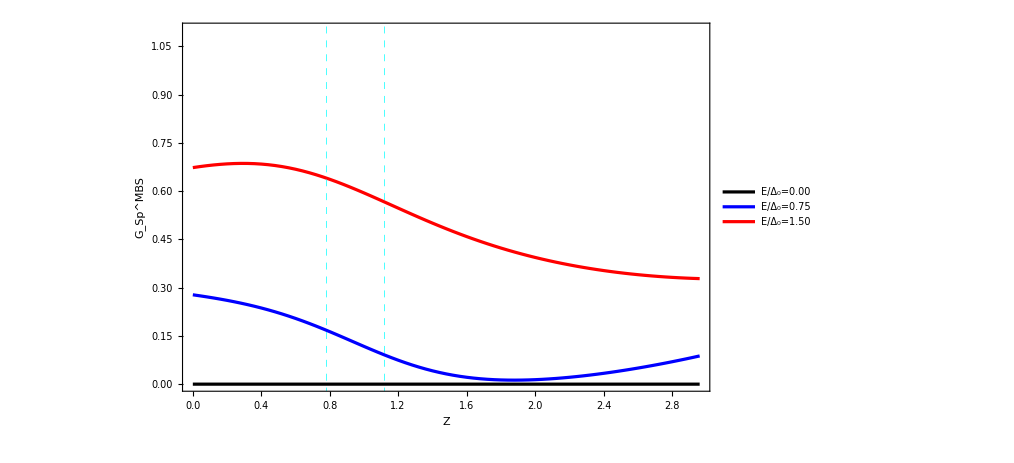

```mathematica
data1=Import["cond3.dat"][[All,{1,8}]];
data2=Import["cond3.dat"][[All,{1,9}]];
data3=Import["cond3.dat"][[All,{1,10}]];
ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{0,1.1},RotateLabel->True,PlotRange->{0,2.1},FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["G_Sp^MBS",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.75",16,Black,Bold],Style["E/Δ_0=1.50",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```

# Differential spin quantum noise at zero kelvin for Z=0.500,0.781 and 1.121 with respect to E/Δ_0 for s=1/2, m = -1/2

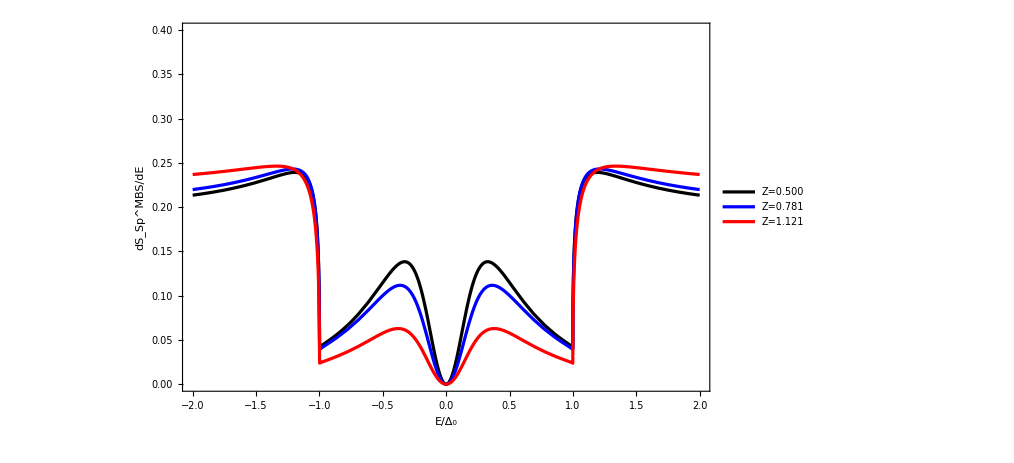

```mathematica
Plot[{(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/.{Z->0.50},(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/.{Z->0.781},(A (1-A)+B (1-B)+2 A*B-4 B1*A2-4 B2*A1+Au (1-Au)+Bu (1-Bu)+2 Au*Bu-4 B1u*A2u-4 B2u*A1u)/2/.{Z->1.121}},{G,-2,2},PlotRange->{0,0.4},RotateLabel->True,FrameLabel->{Style["E/Δ_0",25,Bold,Black],Style[Rotate["dS_Sp^MBS/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["Z=0.500",16,Black,Bold],Style["Z=0.781",16,Black,Bold],Style["Z=1.121",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,15]]
```

# Differential spin quantum noise at zero kelvin for E/Δ_0=0.00,0.75 and 1.50 with respect to Z for s=1/2, m = -1/2

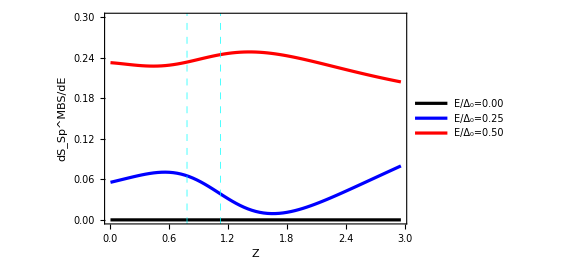

```mathematica
data1=Import["cond3.dat"][[All,{1,11}]];
data2=Import["cond3.dat"][[All,{1,12}]];
data3=Import["cond3.dat"][[All,{1,13}]];
ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{0,0.3},RotateLabel->True,FrameLabel->{Style["Z",25,Bold,Black],Style[Rotate["dS_Sp^MBS/dE",270 Degree],25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],Frame->True,PlotLegends->Placed[{Style["E/Δ_0=0.00",16,Black,Bold],Style["E/Δ_0=0.25",16,Black,Bold],Style["E/Δ_0=0.50",16,Black,Bold]},{Right,Top}],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Black],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],GridLines->{{{0.781,Dashed},{1.121,Dashed}},None},GridLinesStyle->Directive[Cyan,Thick]]
```